## Shear Analysis

L: | 80.1
m: | 400
kappa: | 6.
sigma: | 0.000267
kappa_sigma_r: | 22497.2
Delta: | 0.1
Extension Minimum: | 0
Extension Maximum: | 150
beta: | 4.
mu: | 0.01
c: | 0.14
delta: | 4.3
b: | 0.38
k: | 0.07
ev0: | 1.71
C0: | 0.23
e0: | 0.005001
beta: | 38.6817

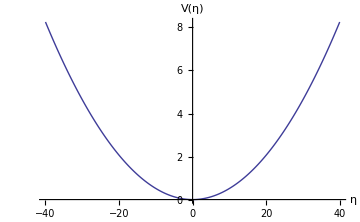

0.1

Backbone spring constant κ:

6.

Residue-pair spring constant σ(ϵ = 0.005001):

0.000267

κ/σ ratio:

22497.2

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

PotentialData = Import["potential_data.out","Table"];

PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];

Subscript[R, pfmxd]=Import["pfmxd_r.out","Table"];
Subscript[R, mxd]=Import["mxd_r.out","Table"];

Subscript[λ, pfmxd]=Import["pfmxd_lambda.out","Table"];
Subscript[λ, mxd]=Import["mxd_lambda.out","Table"];

Subscript[ρ, pfmxd]=Import["pfmxd_roe.out","Table"];
Subscript[ρ, mxd]=Import["mxd_roe.out","Table"];

Parameters=Import["Parameters"];
Grid[Parameters]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

ϵ=Parameters[[17,2]];
β=Parameters[[18,2]];

L=Parameters[[1,2]];
m=Parameters[[2,2]];
Δ=Parameters[[6,2]]
Print["Backbone spring constant κ:"]
κ=Parameters[[3,2]]
Print["Residue-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[4,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[5,2]]
umax=Parameters[[7,2]];
umax=Parameters[[8,2]];

n=ToExpression[StringTrim[Last[StringSplit[Directory[],"/"]],RegularExpression["N*"]]];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

Subscript[η, B]=2.0;

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f (κ/(2β))^(1/2)) ToNewton;
ToDimension[η_]:=η ((κ β)/2)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]](*Å*)
```

2.

0.185659

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

0.0794216

223.094

Partition function & Free Energy

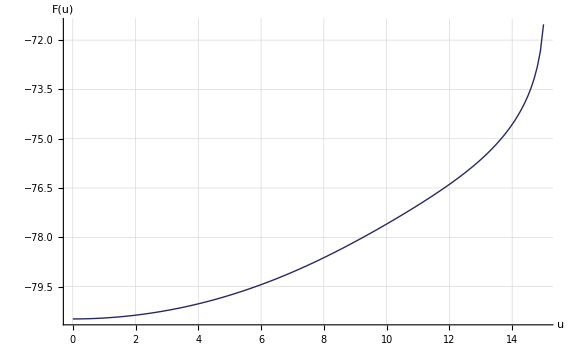
{-Graphics-,-Graphics-}

```mathematica
pIntactPF=ListLinePlot[PartitionFunction,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["Z(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

pIntactFE=ListLinePlot[FreeEnergy,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

{pIntactPF,pIntactFE}
```

Residue-pair separations (x-z), (x-y), (z-y)

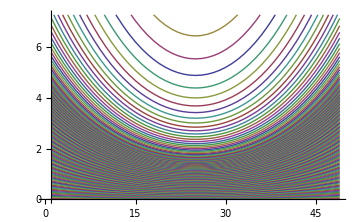
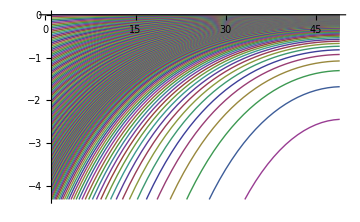

1.99773

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0406498 | 0.0380136 | 0.0355735 | 0.0333169 | 0.0312322 | 0.0293085 | 0.0275361 | 0.0259057 | 0.0244088 | 0.023038 | 0.0217859 | 0.0206462 | 0.019613 | 0.018681 | 0.0178454 | 0.0171017 | 0.0164464 | 0.0158758 | 0.0153871 | 0.0149778 | 0.0146458 | 0.0143893 | 0.014207 | 0.014098 | 0.0140618 | 0.014098 | 0.014207 | 0.0143893 | 0.0146458 | 0.0149778 | 0.0153871 | 0.0158758 | 0.0164463 | 0.0171017 | 0.0178454 | 0.018681 | 0.019613 | 0.0206462 | 0.0217859 | 0.0230379 | 0.0244088 | 0.0259056 | 0.0275361 | 0.0293085 | 0.0312322 | 0.0333169 | 0.0355735 | 0.0380136 | 0.0406498
0.0813027 | 0.0760301 | 0.0711498 | 0.0666364 | 0.0624668 | 0.0586193 | 0.0550743 | 0.0518133 | 0.0488196 | 0.0460777 | 0.0435735 | 0.041294 | 0.0392276 | 0.0373635 | 0.0356921 | 0.0342048 | 0.032894 | 0.0317528 | 0.0307754 | 0.0299568 | 0.0292927 | 0.0287797 | 0.0284151 | 0.0281972 | 0.0281246 | 0.0281972 | 0.0284151 | 0.0287797 | 0.0292927 | 0.0299568 | 0.0307754 | 0.0317528 | 0.032894 | 0.0342048 | 0.0356921 | 0.0373634 | 0.0392276 | 0.041294 | 0.0435734 | 0.0460777 | 0.0488196 | 0.0518133 | 0.0550742 | 0.0586193 | 0.0624667 | 0.0666364 | 0.0711497 | 0.0760301 | 0.0813027
0.121962 | 0.114053 | 0.106732 | 0.099961 | 0.0937062 | 0.0879347 | 0.0826167 | 0.0777249 | 0.0732341 | 0.069121 | 0.0653644 | 0.061945 | 0.0588451 | 0.0560488 | 0.0535416 | 0.0513105 | 0.0493441 | 0.0476323 | 0.0461661 | 0.0449381 | 0.0439419 | 0.0431723 | 0.0426255 | 0.0422985 | 0.0421897 | 0.0422985 | 0.0426255 | 0.0431723 | 0.0439419 | 0.0449381 | 0.0461661 | 0.0476323 | 0.0493441 | 0.0513105 | 0.0535416 | 0.0560488 | 0.0588451 | 0.061945 | 0.0653644 | 0.0691209 | 0.073234 | 0.0777249 | 0.0826167 | 0.0879346 | 0.0937061 | 0.099961 | 0.106731 | 0.114053 | 0.121962
0.162631 | 0.152084 | 0.142322 | 0.133293 | 0.124953 | 0.117257 | 0.110166 | 0.103643 | 0.0976542 | 0.0921696 | 0.0871604 | 0.0826008 | 0.0784673 | 0.0747385 | 0.0713952 | 0.0684202 | 0.0657981 | 0.0635154 | 0.0615604 | 0.0599229 | 0.0585945 | 0.0575683 | 0.0568391 | 0.056403 | 0.0562579 | 0.056403 | 0.0568391 | 0.0575683 | 0.0585945 | 0.0599229 | 0.0615604 | 0.0635154 | 0.0657981 | 0.0684202 | 0.0713952 | 0.0747384 | 0.0784672 | 0.0826008 | 0.0871604 | 0.0921696 | 0.0976542 | 0.103643 | 0.110165 | 0.117257 | 0.124953 | 0.133293 | 0.142321 | 0.152084 | 0.16263
0.203312 | 0.190127 | 0.177922 | 0.166636 | 0.156209 | 0.146588 | 0.137723 | 0.129568 | 0.122082 | 0.115225 | 0.108963 | 0.103263 | 0.0980954 | 0.0934339 | 0.0892543 | 0.0855351 | 0.0822571 | 0.0794035 | 0.0769594 | 0.0749123 | 0.0732516 | 0.0719687 | 0.0710571 | 0.070512 | 0.0703306 | 0.0705119 | 0.0710571 | 0.0719687 | 0.0732515 | 0.0749123 | 0.0769594 | 0.0794035 | 0.0822571 | 0.0855351 | 0.0892543 | 0.0934338 | 0.0980954 | 0.103263 | 0.108963 | 0.115225 | 0.122082 | 0.129568 | 0.137723 | 0.146588 | 0.156209 | 0.166636 | 0.177922 | 0.190127 | 0.203312
0.244008 | 0.228184 | 0.213537 | 0.199991 | 0.187477 | 0.17593 | 0.165291 | 0.155504 | 0.146519 | 0.13829 | 0.130774 | 0.123933 | 0.117731 | 0.112136 | 0.10712 | 0.102657 | 0.0987225 | 0.0952976 | 0.0923643 | 0.0899074 | 0.0879143 | 0.0863746 | 0.0852805 | 0.0846263 | 0.0844086 | 0.0846263 | 0.0852805 | 0.0863746 | 0.0879143 | 0.0899074 | 0.0923643 | 0.0952976 | 0.0987225 | 0.102657 | 0.10712 | 0.112136 | 0.117731 | 0.123933 | 0.130774 | 0.13829 | 0.146519 | 0.155504 | 0.165291 | 0.17593 | 0.187477 | 0.199991 | 0.213537 | 0.228184 | 0.244008
0.284724 | 0.266259 | 0.249168 | 0.233362 | 0.21876 | 0.205286 | 0.192871 | 0.181451 | 0.170967 | 0.161365 | 0.152595 | 0.144613 | 0.137376 | 0.130848 | 0.124994 | 0.119786 | 0.115195 | 0.111199 | 0.107776 | 0.104909 | 0.102584 | 0.100787 | 0.0995105 | 0.0987471 | 0.0984931 | 0.0987471 | 0.0995105 | 0.100787 | 0.102584 | 0.104909 | 0.107776 | 0.111199 | 0.115195 | 0.119786 | 0.124994 | 0.130848 | 0.137376 | 0.144612 | 0.152595 | 0.161365 | 0.170967 | 0.181451 | 0.192871 | 0.205286 | 0.21876 | 0.233362 | 0.249168 | 0.266259 | 0.284724
0.325461 | 0.304355 | 0.284818 | 0.266751 | 0.250059 | 0.234658 | 0.220467 | 0.207413 | 0.195429 | 0.184453 | 0.174428 | 0.165303 | 0.157031 | 0.149569 | 0.142878 | 0.136925 | 0.131677 | 0.127109 | 0.123196 | 0.119919 | 0.117261 | 0.115207 | 0.113748 | 0.112875 | 0.112585 | 0.112875 | 0.113748 | 0.115207 | 0.117261 | 0.119919 | 0.123196 | 0.127109 | 0.131677 | 0.136924 | 0.142878 | 0.149569 | 0.157031 | 0.165303 | 0.174428 | 0.184453 | 0.195428 | 0.207413 | 0.220467 | 0.234658 | 0.250059 | 0.266751 | 0.284818 | 0.304355 | 0.325461
0.366223 | 0.342473 | 0.32049 | 0.30016 | 0.281378 | 0.264047 | 0.248079 | 0.23339 | 0.219905 | 0.207554 | 0.196274 | 0.186006 | 0.176698 | 0.168301 | 0.160773 | 0.154073 | 0.148169 | 0.143029 | 0.138626 | 0.134939 | 0.131947 | 0.129636 | 0.127994 | 0.127012 | 0.126686 | 0.127012 | 0.127994 | 0.129636 | 0.131947 | 0.134939 | 0.138626 | 0.143029 | 0.148169 | 0.154073 | 0.160773 | 0.168301 | 0.176698 | 0.186006 | 0.196274 | 0.207554 | 0.219905 | 0.23339 | 0.248078 | 0.264047 | 0.281377 | 0.300159 | 0.32049 | 0.342473 | 0.366223
0.407013 | 0.380618 | 0.356186 | 0.333591 | 0.312717 | 0.293456 | 0.275709 | 0.259385 | 0.244398 | 0.230671 | 0.218135 | 0.206724 | 0.196379 | 0.187047 | 0.17868 | 0.171234 | 0.164672 | 0.158959 | 0.154066 | 0.149968 | 0.146643 | 0.144075 | 0.14225 | 0.141159 | 0.140796 | 0.141159 | 0.14225 | 0.144075 | 0.146643 | 0.149968 | 0.154066 | 0.158959 | 0.164672 | 0.171234 | 0.178679 | 0.187047 | 0.196379 | 0.206724 | 0.218135 | 0.230671 | 0.244398 | 0.259384 | 0.275709 | 0.293456 | 0.312717 | 0.333591 | 0.356186 | 0.380617 | 0.407013
0.447833 | 0.418791 | 0.391909 | 0.367048 | 0.344081 | 0.322888 | 0.303361 | 0.285399 | 0.268909 | 0.253806 | 0.240012 | 0.227456 | 0.216074 | 0.205806 | 0.1966 | 0.188408 | 0.181187 | 0.174901 | 0.169518 | 0.165009 | 0.161351 | 0.158525 | 0.156517 | 0.155316 | 0.154917 | 0.155316 | 0.156517 | 0.158525 | 0.161351 | 0.165009 | 0.169518 | 0.174901 | 0.181187 | 0.188408 | 0.1966 | 0.205806 | 0.216074 | 0.227456 | 0.240012 | 0.253806 | 0.268909 | 0.285399 | 0.303361 | 0.322888 | 0.34408 | 0.367048 | 0.391908 | 0.418791 | 0.447833
0.488687 | 0.456995 | 0.427661 | 0.400532 | 0.37547 | 0.352344 | 0.331036 | 0.311435 | 0.29344 | 0.27696 | 0.261908 | 0.248206 | 0.235786 | 0.224581 | 0.214535 | 0.205595 | 0.197716 | 0.190857 | 0.184982 | 0.180062 | 0.17607 | 0.172987 | 0.170795 | 0.169485 | 0.169049 | 0.169485 | 0.170795 | 0.172987 | 0.17607 | 0.180062 | 0.184982 | 0.190857 | 0.197716 | 0.205595 | 0.214535 | 0.224581 | 0.235786 | 0.248206 | 0.261907 | 0.27696 | 0.29344 | 0.311435 | 0.331035 | 0.352344 | 0.37547 | 0.400532 | 0.427661 | 0.456995 | 0.488687
0.529578 | 0.495234 | 0.463445 | 0.434046 | 0.406887 | 0.381826 | 0.358734 | 0.337494 | 0.317994 | 0.300134 | 0.283822 | 0.268975 | 0.255515 | 0.243373 | 0.232486 | 0.222798 | 0.21426 | 0.206827 | 0.200461 | 0.195128 | 0.190802 | 0.187461 | 0.185086 | 0.183667 | 0.183194 | 0.183667 | 0.185086 | 0.187461 | 0.190802 | 0.195128 | 0.20046 | 0.206827 | 0.21426 | 0.222798 | 0.232486 | 0.243372 | 0.255515 | 0.268975 | 0.283822 | 0.300134 | 0.317994 | 0.337494 | 0.358734 | 0.381826 | 0.406887 | 0.434046 | 0.463445 | 0.495234 | 0.529577
0.570507 | 0.533509 | 0.499263 | 0.467593 | 0.438334 | 0.411336 | 0.38646 | 0.363578 | 0.342571 | 0.323331 | 0.305758 | 0.289763 | 0.275263 | 0.262182 | 0.250454 | 0.240018 | 0.23082 | 0.222812 | 0.215954 | 0.210209 | 0.205549 | 0.201949 | 0.199391 | 0.197862 | 0.197353 | 0.197862 | 0.199391 | 0.201949 | 0.205549 | 0.210209 | 0.215954 | 0.222812 | 0.23082 | 0.240018 | 0.250454 | 0.262182 | 0.275263 | 0.289763 | 0.305758 | 0.32333 | 0.34257 | 0.363578 | 0.38646 | 0.411336 | 0.438334 | 0.467592 | 0.499263 | 0.533509 | 0.570507
0.611479 | 0.571824 | 0.535119 | 0.501173 | 0.469813 | 0.440877 | 0.414214 | 0.389688 | 0.367173 | 0.346551 | 0.327717 | 0.310573 | 0.295031 | 0.281011 | 0.268441 | 0.257255 | 0.247396 | 0.238813 | 0.231463 | 0.225306 | 0.220311 | 0.216453 | 0.213711 | 0.212071 | 0.211526 | 0.212071 | 0.213711 | 0.216453 | 0.220311 | 0.225306 | 0.231462 | 0.238813 | 0.247396 | 0.257255 | 0.268441 | 0.281011 | 0.295031 | 0.310573 | 0.327717 | 0.346551 | 0.367173 | 0.389688 | 0.414214 | 0.440877 | 0.469813 | 0.501173 | 0.535118 | 0.571824 | 0.611479
0.652495 | 0.61018 | 0.571013 | 0.534791 | 0.501327 | 0.470449 | 0.441999 | 0.415828 | 0.391802 | 0.369797 | 0.349699 | 0.331405 | 0.314821 | 0.299861 | 0.286447 | 0.274511 | 0.263991 | 0.254832 | 0.246988 | 0.240419 | 0.235089 | 0.230972 | 0.228046 | 0.226296 | 0.225714 | 0.226296 | 0.228046 | 0.230972 | 0.235089 | 0.240418 | 0.246988 | 0.254832 | 0.263991 | 0.274511 | 0.286447 | 0.29986 | 0.314821 | 0.331405 | 0.349699 | 0.369796 | 0.391801 | 0.415827 | 0.441998 | 0.470449 | 0.501327 | 0.53479 | 0.571012 | 0.61018 | 0.652495
0.693559 | 0.64858 | 0.606948 | 0.568446 | 0.532877 | 0.500056 | 0.469815 | 0.441997 | 0.416459 | 0.393069 | 0.371707 | 0.352262 | 0.334633 | 0.318732 | 0.304474 | 0.291787 | 0.280604 | 0.27087 | 0.262532 | 0.255549 | 0.249884 | 0.245507 | 0.242397 | 0.240538 | 0.239919 | 0.240538 | 0.242397 | 0.245507 | 0.249884 | 0.255549 | 0.262532 | 0.27087 | 0.280604 | 0.291787 | 0.304474 | 0.318732 | 0.334633 | 0.352261 | 0.371706 | 0.393069 | 0.416459 | 0.441997 | 0.469815 | 0.500056 | 0.532877 | 0.568446 | 0.606948 | 0.64858 | 0.693558
0.734672 | 0.687027 | 0.642927 | 0.602143 | 0.564465 | 0.529699 | 0.497665 | 0.468198 | 0.441146 | 0.416369 | 0.393741 | 0.373143 | 0.35447 | 0.337626 | 0.322523 | 0.309083 | 0.297238 | 0.286926 | 0.278095 | 0.270697 | 0.264696 | 0.260061 | 0.256766 | 0.254797 | 0.254141 | 0.254797 | 0.256766 | 0.260061 | 0.264696 | 0.270697 | 0.278095 | 0.286926 | 0.297238 | 0.309083 | 0.322522 | 0.337625 | 0.35447 | 0.373143 | 0.393741 | 0.416369 | 0.441146 | 0.468198 | 0.497665 | 0.529699 | 0.564465 | 0.602143 | 0.642927 | 0.687027 | 0.734671
0.775837 | 0.725523 | 0.678952 | 0.635883 | 0.596093 | 0.559379 | 0.52555 | 0.494432 | 0.465864 | 0.4397 | 0.415803 | 0.394051 | 0.374332 | 0.356543 | 0.340594 | 0.326402 | 0.313893 | 0.303004 | 0.293677 | 0.285865 | 0.279528 | 0.274632 | 0.271154 | 0.269073 | 0.268381 | 0.269073 | 0.271154 | 0.274632 | 0.279528 | 0.285865 | 0.293677 | 0.303003 | 0.313893 | 0.326402 | 0.340594 | 0.356543 | 0.374332 | 0.394051 | 0.415803 | 0.439699 | 0.465864 | 0.494432 | 0.52555 | 0.559379 | 0.596093 | 0.635882 | 0.678951 | 0.725523 | 0.775836
0.817056 | 0.76407 | 0.715024 | 0.669667 | 0.627763 | 0.589098 | 0.553472 | 0.520701 | 0.490615 | 0.46306 | 0.437894 | 0.414987 | 0.39422 | 0.375486 | 0.35869 | 0.343743 | 0.33057 | 0.319102 | 0.30928 | 0.301053 | 0.294379 | 0.289223 | 0.28556 | 0.283369 | 0.28264 | 0.283369 | 0.28556 | 0.289223 | 0.294379 | 0.301053 | 0.30928 | 0.319102 | 0.33057 | 0.343743 | 0.35869 | 0.375486 | 0.39422 | 0.414987 | 0.437894 | 0.46306 | 0.490615 | 0.520701 | 0.553472 | 0.589098 | 0.627763 | 0.669666 | 0.715024 | 0.764069 | 0.817056
0.858333 | 0.802669 | 0.751146 | 0.703497 | 0.659477 | 0.618859 | 0.581433 | 0.547006 | 0.5154 | 0.486453 | 0.460016 | 0.435951 | 0.414135 | 0.394455 | 0.37681 | 0.361109 | 0.34727 | 0.335222 | 0.324904 | 0.316261 | 0.30925 | 0.303834 | 0.299986 | 0.297684 | 0.296919 | 0.297684 | 0.299986 | 0.303834 | 0.30925 | 0.316261 | 0.324904 | 0.335222 | 0.34727 | 0.361109 | 0.37681 | 0.394455 | 0.414135 | 0.435951 | 0.460016 | 0.486453 | 0.5154 | 0.547005 | 0.581432 | 0.618858 | 0.659477 | 0.703497 | 0.751145 | 0.802669 | 0.858332
0.899668 | 0.841324 | 0.787319 | 0.737375 | 0.691236 | 0.648661 | 0.609433 | 0.573348 | 0.540221 | 0.50988 | 0.482169 | 0.456945 | 0.434079 | 0.413451 | 0.394956 | 0.378499 | 0.363993 | 0.351366 | 0.34055 | 0.331492 | 0.324143 | 0.318466 | 0.314432 | 0.31202 | 0.311217 | 0.31202 | 0.314432 | 0.318466 | 0.324143 | 0.331492 | 0.34055 | 0.351366 | 0.363993 | 0.378499 | 0.394956 | 0.413451 | 0.434079 | 0.456945 | 0.482169 | 0.50988 | 0.54022 | 0.573348 | 0.609433 | 0.648661 | 0.691235 | 0.737375 | 0.787319 | 0.841323 | 0.899667
0.941064 | 0.880035 | 0.823545 | 0.771304 | 0.723041 | 0.678508 | 0.637474 | 0.599729 | 0.565077 | 0.533341 | 0.504355 | 0.47797 | 0.454052 | 0.432475 | 0.413129 | 0.395914 | 0.380742 | 0.367533 | 0.35622 | 0.346745 | 0.339058 | 0.33312 | 0.3289 | 0.326377 | 0.325537 | 0.326377 | 0.3289 | 0.33312 | 0.339058 | 0.346744 | 0.35622 | 0.367533 | 0.380742 | 0.395914 | 0.413129 | 0.432475 | 0.454052 | 0.47797 | 0.504355 | 0.53334 | 0.565077 | 0.599729 | 0.637474 | 0.678507 | 0.723041 | 0.771304 | 0.823545 | 0.880034 | 0.941063
0.982522 | 0.918805 | 0.859826 | 0.805283 | 0.754894 | 0.708399 | 0.665558 | 0.62615 | 0.589972 | 0.556837 | 0.526574 | 0.499027 | 0.474055 | 0.451528 | 0.43133 | 0.413356 | 0.397515 | 0.383725 | 0.371913 | 0.36202 | 0.353995 | 0.347795 | 0.34339 | 0.340755 | 0.339879 | 0.340755 | 0.34339 | 0.347795 | 0.353995 | 0.36202 | 0.371913 | 0.383724 | 0.397515 | 0.413356 | 0.431329 | 0.451527 | 0.474055 | 0.499027 | 0.526574 | 0.556837 | 0.589972 | 0.62615 | 0.665558 | 0.708399 | 0.754894 | 0.805283 | 0.859826 | 0.918804 | 0.982522
1.02404 | 0.957634 | 0.896164 | 0.839316 | 0.786797 | 0.738337 | 0.693685 | 0.652612 | 0.614905 | 0.580369 | 0.548828 | 0.520117 | 0.494089 | 0.47061 | 0.449558 | 0.430825 | 0.414315 | 0.399941 | 0.387631 | 0.37732 | 0.368955 | 0.362494 | 0.357902 | 0.355156 | 0.354243 | 0.355156 | 0.357902 | 0.362494 | 0.368955 | 0.37732 | 0.387631 | 0.399941 | 0.414315 | 0.430825 | 0.449558 | 0.47061 | 0.494089 | 0.520117 | 0.548828 | 0.580369 | 0.614905 | 0.652612 | 0.693685 | 0.738337 | 0.786797 | 0.839316 | 0.896163 | 0.957634 | 1.02404
1.06563 | 0.996526 | 0.932559 | 0.873402 | 0.818751 | 0.768323 | 0.721858 | 0.679116 | 0.639877 | 0.603939 | 0.571117 | 0.54124 | 0.514155 | 0.489722 | 0.467816 | 0.448322 | 0.431141 | 0.416184 | 0.403373 | 0.392643 | 0.383939 | 0.377215 | 0.372437 | 0.36958 | 0.368629 | 0.36958 | 0.372437 | 0.377215 | 0.383939 | 0.392643 | 0.403373 | 0.416184 | 0.431141 | 0.448322 | 0.467815 | 0.489722 | 0.514155 | 0.54124 | 0.571117 | 0.603939 | 0.639877 | 0.679116 | 0.721857 | 0.768322 | 0.81875 | 0.873402 | 0.932559 | 0.996526 | 1.06563
1.10729 | 1.03548 | 0.969013 | 0.907544 | 0.850756 | 0.798356 | 0.750075 | 0.705663 | 0.66489 | 0.627548 | 0.593442 | 0.562397 | 0.534254 | 0.508866 | 0.486103 | 0.465847 | 0.447994 | 0.432452 | 0.419141 | 0.407992 | 0.398947 | 0.391961 | 0.386996 | 0.384027 | 0.383039 | 0.384027 | 0.386996 | 0.391961 | 0.398947 | 0.407992 | 0.419141 | 0.432452 | 0.447994 | 0.465847 | 0.486102 | 0.508866 | 0.534253 | 0.562397 | 0.593442 | 0.627547 | 0.66489 | 0.705662 | 0.750075 | 0.798356 | 0.850756 | 0.907543 | 0.969013 | 1.03548 | 1.10729
1.14901 | 1.0745 | 1.00553 | 0.941742 | 0.882814 | 0.82844 | 0.778339 | 0.732253 | 0.689945 | 0.651195 | 0.615804 | 0.583589 | 0.554385 | 0.52804 | 0.50442 | 0.483401 | 0.464875 | 0.448748 | 0.434935 | 0.423366 | 0.41398 | 0.40673 | 0.401578 | 0.398498 | 0.397472 | 0.398498 | 0.401578 | 0.40673 | 0.41398 | 0.423366 | 0.434935 | 0.448748 | 0.464875 | 0.483401 | 0.50442 | 0.52804 | 0.554385 | 0.583589 | 0.615803 | 0.651194 | 0.689944 | 0.732253 | 0.778339 | 0.82844 | 0.882813 | 0.941741 | 1.00553 | 1.0745 | 1.14901
1.19081 | 1.11358 | 1.0421 | 0.975996 | 0.914925 | 0.858573 | 0.80665 | 0.758888 | 0.71504 | 0.674881 | 0.638203 | 0.604817 | 0.57455 | 0.547247 | 0.522767 | 0.500984 | 0.481785 | 0.465071 | 0.450755 | 0.438765 | 0.429038 | 0.421525 | 0.416185 | 0.412992 | 0.41193 | 0.412992 | 0.416185 | 0.421525 | 0.429038 | 0.438765 | 0.450755 | 0.46507 | 0.481785 | 0.500984 | 0.522767 | 0.547247 | 0.57455 | 0.604816 | 0.638203 | 0.674881 | 0.71504 | 0.758888 | 0.80665 | 0.858573 | 0.914925 | 0.975996 | 1.0421 | 1.11358 | 1.19081
1.23267 | 1.15273 | 1.07874 | 1.01031 | 0.947091 | 0.888758 | 0.835009 | 0.785568 | 0.740179 | 0.698607 | 0.66064 | 0.62608 | 0.594749 | 0.566487 | 0.541146 | 0.518597 | 0.498723 | 0.481421 | 0.466602 | 0.454191 | 0.444122 | 0.436344 | 0.430817 | 0.427512 | 0.426412 | 0.427512 | 0.430817 | 0.436344 | 0.444122 | 0.454191 | 0.466602 | 0.481421 | 0.498722 | 0.518597 | 0.541146 | 0.566486 | 0.594749 | 0.62608 | 0.66064 | 0.698607 | 0.740178 | 0.785568 | 0.835009 | 0.888757 | 0.94709 | 1.01031 | 1.07874 | 1.15273 | 1.23267
1.27461 | 1.19195 | 1.11544 | 1.04468 | 0.979311 | 0.918993 | 0.863416 | 0.812293 | 0.76536 | 0.722374 | 0.683115 | 0.647379 | 0.614983 | 0.585759 | 0.559556 | 0.536239 | 0.515689 | 0.497799 | 0.482476 | 0.469642 | 0.459231 | 0.451188 | 0.445473 | 0.442056 | 0.440919 | 0.442056 | 0.445473 | 0.451188 | 0.459231 | 0.469642 | 0.482476 | 0.497799 | 0.515689 | 0.536239 | 0.559556 | 0.585758 | 0.614983 | 0.647379 | 0.683115 | 0.722374 | 0.765359 | 0.812293 | 0.863416 | 0.918993 | 0.97931 | 1.04468 | 1.11544 | 1.19195 | 1.27461
1.31662 | 1.23123 | 1.1522 | 1.07911 | 1.01159 | 0.949281 | 0.891872 | 0.839064 | 0.790584 | 0.746181 | 0.705628 | 0.668715 | 0.635251 | 0.605063 | 0.577997 | 0.553912 | 0.532685 | 0.514205 | 0.498377 | 0.48512 | 0.474366 | 0.466058 | 0.460155 | 0.456625 | 0.45545 | 0.456624 | 0.460155 | 0.466058 | 0.474366 | 0.48512 | 0.498377 | 0.514205 | 0.532685 | 0.553912 | 0.577997 | 0.605063 | 0.635251 | 0.668715 | 0.705628 | 0.746181 | 0.790583 | 0.839063 | 0.891872 | 0.94928 | 1.01159 | 1.07911 | 1.1522 | 1.23123 | 1.31661
1.35869 | 1.27058 | 1.18902 | 1.1136 | 1.04392 | 0.97962 | 0.920376 | 0.86588 | 0.815851 | 0.770029 | 0.72818 | 0.690087 | 0.655553 | 0.624401 | 0.59647 | 0.571615 | 0.549709 | 0.530639 | 0.514305 | 0.500625 | 0.489527 | 0.480953 | 0.474861 | 0.471218 | 0.470006 | 0.471218 | 0.474861 | 0.480953 | 0.489526 | 0.500625 | 0.514305 | 0.530639 | 0.549709 | 0.571615 | 0.59647 | 0.624401 | 0.655553 | 0.690087 | 0.72818 | 0.770029 | 0.81585 | 0.86588 | 0.920376 | 0.979619 | 1.04392 | 1.1136 | 1.18902 | 1.27058 | 1.35869
1.40084 | 1.31 | 1.22591 | 1.14814 | 1.0763 | 1.01001 | 0.948929 | 0.892742 | 0.841161 | 0.793918 | 0.75077 | 0.711495 | 0.675891 | 0.643772 | 0.614974 | 0.589349 | 0.566763 | 0.547101 | 0.530261 | 0.516156 | 0.504713 | 0.495874 | 0.489593 | 0.485837 | 0.484587 | 0.485837 | 0.489593 | 0.495874 | 0.504713 | 0.516156 | 0.53026 | 0.547101 | 0.566763 | 0.589348 | 0.614974 | 0.643772 | 0.67589 | 0.711495 | 0.75077 | 0.793918 | 0.84116 | 0.892742 | 0.948929 | 1.01001 | 1.0763 | 1.14814 | 1.22591 | 1.31 | 1.40084
1.44307 | 1.34948 | 1.26286 | 1.18275 | 1.10874 | 1.04045 | 0.97753 | 0.91965 | 0.866514 | 0.817847 | 0.773399 | 0.73294 | 0.696262 | 0.663176 | 0.63351 | 0.607112 | 0.583845 | 0.563591 | 0.546243 | 0.531713 | 0.519925 | 0.51082 | 0.504349 | 0.50048 | 0.499193 | 0.50048 | 0.504349 | 0.51082 | 0.519925 | 0.531713 | 0.546243 | 0.56359 | 0.583845 | 0.607112 | 0.63351 | 0.663176 | 0.696262 | 0.73294 | 0.773399 | 0.817847 | 0.866514 | 0.91965 | 0.97753 | 1.04045 | 1.10874 | 1.18275 | 1.26286 | 1.34948 | 1.44307
1.48536 | 1.38903 | 1.29987 | 1.21741 | 1.14124 | 1.07095 | 1.00618 | 0.946603 | 0.891909 | 0.841816 | 0.796066 | 0.754421 | 0.716668 | 0.682612 | 0.652077 | 0.624905 | 0.600957 | 0.580108 | 0.562252 | 0.547296 | 0.535163 | 0.525791 | 0.519131 | 0.515148 | 0.513823 | 0.515148 | 0.519131 | 0.525791 | 0.535163 | 0.547296 | 0.562252 | 0.580108 | 0.600957 | 0.624905 | 0.652076 | 0.682612 | 0.716668 | 0.754421 | 0.796065 | 0.841816 | 0.891909 | 0.946603 | 1.00618 | 1.07095 | 1.14124 | 1.21741 | 1.29987 | 1.38903 | 1.48536
1.52772 | 1.42865 | 1.33694 | 1.25214 | 1.17379 | 1.10149 | 1.03488 | 0.9736 | 0.917347 | 0.865825 | 0.81877 | 0.775938 | 0.737108 | 0.70208 | 0.670674 | 0.642727 | 0.618096 | 0.596653 | 0.578288 | 0.562905 | 0.550426 | 0.540787 | 0.533936 | 0.52984 | 0.528477 | 0.529841 | 0.533936 | 0.540787 | 0.550426 | 0.562905 | 0.578288 | 0.596653 | 0.618096 | 0.642727 | 0.670674 | 0.70208 | 0.737108 | 0.775937 | 0.818769 | 0.865825 | 0.917347 | 0.9736 | 1.03488 | 1.10149 | 1.17378 | 1.25213 | 1.33694 | 1.42865 | 1.52772
1.57015 | 1.46833 | 1.37408 | 1.28691 | 1.20639 | 1.13208 | 1.06362 | 1.00064 | 0.942826 | 0.889873 | 0.841511 | 0.797489 | 0.757581 | 0.72158 | 0.689302 | 0.660579 | 0.635263 | 0.613225 | 0.594349 | 0.57854 | 0.565714 | 0.555807 | 0.548766 | 0.544557 | 0.543156 | 0.544557 | 0.548766 | 0.555807 | 0.565714 | 0.57854 | 0.594349 | 0.613225 | 0.635263 | 0.660579 | 0.689302 | 0.72158 | 0.75758 | 0.797489 | 0.84151 | 0.889873 | 0.942826 | 1.00064 | 1.06362 | 1.13208 | 1.20639 | 1.28691 | 1.37408 | 1.46833 | 1.57015
1.61265 | 1.50807 | 1.41127 | 1.32175 | 1.23904 | 1.16272 | 1.09241 | 1.02773 | 0.968345 | 0.913959 | 0.864288 | 0.819074 | 0.778086 | 0.741111 | 0.707959 | 0.678459 | 0.652458 | 0.629823 | 0.610437 | 0.594199 | 0.581026 | 0.570851 | 0.56362 | 0.559296 | 0.557857 | 0.559296 | 0.56362 | 0.570851 | 0.581026 | 0.594199 | 0.610436 | 0.629823 | 0.652458 | 0.678459 | 0.707959 | 0.741111 | 0.778086 | 0.819074 | 0.864288 | 0.913959 | 0.968345 | 1.02773 | 1.09241 | 1.16272 | 1.23904 | 1.32175 | 1.41127 | 1.50807 | 1.61265
1.65522 | 1.54788 | 1.44852 | 1.35663 | 1.27174 | 1.19341 | 1.12124 | 1.05485 | 0.993904 | 0.938082 | 0.8871 | 0.840693 | 0.798623 | 0.760672 | 0.726645 | 0.696366 | 0.669679 | 0.646446 | 0.626549 | 0.609882 | 0.596362 | 0.585918 | 0.578496 | 0.574058 | 0.572581 | 0.574058 | 0.578496 | 0.585918 | 0.596362 | 0.609882 | 0.626548 | 0.646446 | 0.669679 | 0.696366 | 0.726645 | 0.760672 | 0.798623 | 0.840693 | 0.8871 | 0.938082 | 0.993903 | 1.05485 | 1.12124 | 1.19341 | 1.27174 | 1.35663 | 1.44852 | 1.54787 | 1.65522
1.69785 | 1.58774 | 1.48582 | 1.39157 | 1.30449 | 1.22415 | 1.15012 | 1.08202 | 1.0195 | 0.962241 | 0.909946 | 0.862344 | 0.81919 | 0.780262 | 0.745359 | 0.7143 | 0.686926 | 0.663095 | 0.642684 | 0.625589 | 0.61172 | 0.601007 | 0.593394 | 0.588842 | 0.587327 | 0.588842 | 0.593394 | 0.601007 | 0.61172 | 0.625589 | 0.642684 | 0.663095 | 0.686925 | 0.7143 | 0.745358 | 0.780262 | 0.81919 | 0.862344 | 0.909945 | 0.962241 | 1.0195 | 1.08202 | 1.15012 | 1.22415 | 1.30449 | 1.39157 | 1.48582 | 1.58774 | 1.69785
1.74053 | 1.62766 | 1.52318 | 1.42656 | 1.33729 | 1.25493 | 1.17903 | 1.10922 | 1.04513 | 0.986434 | 0.932824 | 0.884025 | 0.839787 | 0.79988 | 0.764099 | 0.732259 | 0.704197 | 0.679767 | 0.658843 | 0.641318 | 0.627101 | 0.616118 | 0.608314 | 0.603647 | 0.602094 | 0.603647 | 0.608314 | 0.616118 | 0.6271 | 0.641318 | 0.658843 | 0.679767 | 0.704197 | 0.732259 | 0.764098 | 0.79988 | 0.839786 | 0.884025 | 0.932824 | 0.986434 | 1.04513 | 1.10922 | 1.17903 | 1.25493 | 1.33729 | 1.42656 | 1.52318 | 1.62766 | 1.74053
1.78328 | 1.66763 | 1.56059 | 1.46159 | 1.37014 | 1.28575 | 1.20799 | 1.13646 | 1.0708 | 1.01066 | 0.955733 | 0.905736 | 0.860411 | 0.819524 | 0.782864 | 0.750243 | 0.721491 | 0.696461 | 0.675023 | 0.657068 | 0.642501 | 0.631249 | 0.623253 | 0.618472 | 0.616881 | 0.618472 | 0.623253 | 0.631249 | 0.642501 | 0.657068 | 0.675023 | 0.696461 | 0.721491 | 0.750242 | 0.782864 | 0.819524 | 0.860411 | 0.905736 | 0.955733 | 1.01066 | 1.0708 | 1.13646 | 1.20799 | 1.28575 | 1.37014 | 1.46159 | 1.56059 | 1.66763 | 1.78328
1.82608 | 1.70766 | 1.59804 | 1.49667 | 1.40302 | 1.3166 | 1.23698 | 1.16374 | 1.0965 | 1.03492 | 0.978671 | 0.927474 | 0.881061 | 0.839193 | 0.801653 | 0.768249 | 0.738807 | 0.713176 | 0.691224 | 0.672838 | 0.657922 | 0.646399 | 0.638211 | 0.633315 | 0.631686 | 0.633316 | 0.638211 | 0.646399 | 0.657922 | 0.672838 | 0.691224 | 0.713176 | 0.738807 | 0.768249 | 0.801653 | 0.839192 | 0.881061 | 0.927474 | 0.978671 | 1.03492 | 1.0965 | 1.16374 | 1.23698 | 1.3166 | 1.40302 | 1.49667 | 1.59804 | 1.70766 | 1.82608
1.86893 | 1.74773 | 1.63554 | 1.53179 | 1.43594 | 1.3475 | 1.26601 | 1.19105 | 1.12223 | 1.0592 | 1.00164 | 0.949237 | 0.901735 | 0.858885 | 0.820464 | 0.786276 | 0.756143 | 0.729911 | 0.707444 | 0.688626 | 0.67336 | 0.661567 | 0.653187 | 0.648176 | 0.646509 | 0.648176 | 0.653187 | 0.661567 | 0.67336 | 0.688626 | 0.707444 | 0.729911 | 0.756143 | 0.786276 | 0.820464 | 0.858884 | 0.901735 | 0.949237 | 1.00164 | 1.0592 | 1.12223 | 1.19105 | 1.26601 | 1.3475 | 1.43594 | 1.53179 | 1.63554 | 1.74773 | 1.86893
1.91182 | 1.78784 | 1.67308 | 1.56695 | 1.4689 | 1.37843 | 1.29506 | 1.21838 | 1.14799 | 1.08351 | 1.02462 | 0.971024 | 0.922431 | 0.878597 | 0.839295 | 0.804322 | 0.773498 | 0.746664 | 0.723681 | 0.704431 | 0.688815 | 0.676751 | 0.668179 | 0.663053 | 0.661347 | 0.663053 | 0.668179 | 0.676751 | 0.688815 | 0.704431 | 0.723681 | 0.746664 | 0.773498 | 0.804322 | 0.839295 | 0.878597 | 0.922431 | 0.971024 | 1.02462 | 1.08351 | 1.14799 | 1.21838 | 1.29506 | 1.37843 | 1.4689 | 1.56695 | 1.67308 | 1.78784 | 1.91182
1.95476 | 1.82799 | 1.71065 | 1.60214 | 1.50189 | 1.40938 | 1.32415 | 1.24575 | 1.17377 | 1.10784 | 1.04764 | 0.992831 | 0.943147 | 0.898329 | 0.858144 | 0.822385 | 0.790869 | 0.763432 | 0.739933 | 0.720251 | 0.704284 | 0.69195 | 0.683185 | 0.677944 | 0.6762 | 0.677944 | 0.683185 | 0.69195 | 0.704284 | 0.720251 | 0.739933 | 0.763432 | 0.790869 | 0.822385 | 0.858144 | 0.898328 | 0.943147 | 0.992831 | 1.04764 | 1.10784 | 1.17377 | 1.24574 | 1.32415 | 1.40938 | 1.50189 | 1.60214 | 1.71065 | 1.82799 | 1.95476
1.99773 | 1.86817 | 1.74826 | 1.63736 | 1.5349 | 1.44036 | 1.35326 | 1.27313 | 1.19957 | 1.1322 | 1.07067 | 1.01466 | 0.96388 | 0.918076 | 0.877008 | 0.840463 | 0.808254 | 0.780214 | 0.756199 | 0.736084 | 0.719766 | 0.70716 | 0.698203 | 0.692847 | 0.691064 | 0.692847 | 0.698203 | 0.70716 | 0.719766 | 0.736084 | 0.756199 | 0.780214 | 0.808254 | 0.840463 | 0.877008 | 0.918076 | 0.96388 | 1.01466 | 1.07066 | 1.1322 | 1.19957 | 1.27313 | 1.35326 | 1.44036 | 1.5349 | 1.63736 | 1.74826 | 1.86817 | 1.99773
2.04073 | 1.90838 | 1.78589 | 1.6726 | 1.56794 | 1.47137 | 1.38238 | 1.30053 | 1.22539 | 1.15657 | 1.09371 | 1.0365 | 0.984627 | 0.937837 | 0.895885 | 0.858554 | 0.825651 | 0.797008 | 0.772475 | 0.751927 | 0.735258 | 0.722381 | 0.713231 | 0.707759 | 0.705939 | 0.707759 | 0.713231 | 0.722381 | 0.735258 | 0.751927 | 0.772475 | 0.797007 | 0.825651 | 0.858553 | 0.895884 | 0.937837 | 0.984626 | 1.03649 | 1.09371 | 1.15657 | 1.22539 | 1.30053 | 1.38238 | 1.47137 | 1.56794 | 1.6726 | 1.78589 | 1.90838 | 2.04073
2.08375 | 1.94862 | 1.82353 | 1.70786 | 1.60099 | 1.50239 | 1.41153 | 1.32795 | 1.25122 | 1.18095 | 1.11677 | 1.05835 | 1.00538 | 0.957608 | 0.914771 | 0.876653 | 0.843057 | 0.81381 | 0.78876 | 0.767779 | 0.750758 | 0.73761 | 0.728267 | 0.72268 | 0.720821 | 0.72268 | 0.728267 | 0.73761 | 0.750758 | 0.767779 | 0.78876 | 0.81381 | 0.843057 | 0.876653 | 0.914771 | 0.957608 | 1.00538 | 1.05835 | 1.11677 | 1.18095 | 1.25122 | 1.32795 | 1.41153 | 1.50239 | 1.60099 | 1.70786 | 1.82353 | 1.94862 | 2.08375
2.12679 | 1.98886 | 1.8612 | 1.74313 | 1.63406 | 1.53341 | 1.44068 | 1.35538 | 1.27706 | 1.20534 | 1.13983 | 1.0802 | 1.02615 | 0.977386 | 0.933664 | 0.894759 | 0.860469 | 0.830618 | 0.805051 | 0.783636 | 0.766264 | 0.752844 | 0.743308 | 0.737606 | 0.735708 | 0.737606 | 0.743308 | 0.752844 | 0.766264 | 0.783636 | 0.80505 | 0.830617 | 0.860469 | 0.894759 | 0.933664 | 0.977385 | 1.02615 | 1.0802 | 1.13983 | 1.20534 | 1.27706 | 1.35538 | 1.44068 | 1.53341 | 1.63406 | 1.74313 | 1.8612 | 1.98886 | 2.12679
2.16983 | 2.02911 | 1.89887 | 1.77841 | 1.66713 | 1.56445 | 1.46984 | 1.38281 | 1.30291 | 1.22973 | 1.1629 | 1.10207 | 1.04692 | 0.997167 | 0.952561 | 0.912868 | 0.877884 | 0.847428 | 0.821344 | 0.799496 | 0.781772 | 0.768081 | 0.758352 | 0.752534 | 0.750598 | 0.752534 | 0.758352 | 0.768081 | 0.781772 | 0.799496 | 0.821344 | 0.847428 | 0.877884 | 0.912868 | 0.95256 | 0.997167 | 1.04692 | 1.10207 | 1.1629 | 1.22973 | 1.30291 | 1.38281 | 1.46984 | 1.56445 | 1.66713 | 1.77841 | 1.89886 | 2.02911 | 2.16983
2.21287 | 2.06936 | 1.93653 | 1.81369 | 1.7002 | 1.59548 | 1.49899 | 1.41024 | 1.32876 | 1.25413 | 1.18597 | 1.12393 | 1.06768 | 1.01695 | 0.971456 | 0.930976 | 0.895298 | 0.864238 | 0.837636 | 0.815355 | 0.79728 | 0.783317 | 0.773395 | 0.767462 | 0.765488 | 0.767462 | 0.773395 | 0.783317 | 0.79728 | 0.815355 | 0.837636 | 0.864238 | 0.895298 | 0.930976 | 0.971456 | 1.01695 | 1.06768 | 1.12393 | 1.18597 | 1.25413 | 1.32876 | 1.41024 | 1.49899 | 1.59548 | 1.7002 | 1.81369 | 1.93653 | 2.06936 | 2.21287
2.2559 | 2.10961 | 1.97419 | 1.84896 | 1.73326 | 1.62651 | 1.52814 | 1.43766 | 1.3546 | 1.27852 | 1.20903 | 1.14578 | 1.08845 | 1.03672 | 0.990347 | 0.94908 | 0.912708 | 0.881044 | 0.853925 | 0.831211 | 0.812784 | 0.79855 | 0.788434 | 0.782386 | 0.780373 | 0.782386 | 0.788434 | 0.798549 | 0.812784 | 0.831211 | 0.853925 | 0.881044 | 0.912708 | 0.94908 | 0.990347 | 1.03672 | 1.08845 | 1.14578 | 1.20903 | 1.27852 | 1.35459 | 1.43766 | 1.52814 | 1.62651 | 1.73326 | 1.84896 | 1.97419 | 2.10961 | 2.2559
2.29891 | 2.14983 | 2.01183 | 1.88421 | 1.76631 | 1.65752 | 1.55728 | 1.46507 | 1.38042 | 1.30289 | 1.23208 | 1.16763 | 1.1092 | 1.05649 | 1.00923 | 0.967175 | 0.93011 | 0.897842 | 0.870206 | 0.847059 | 0.82828 | 0.813775 | 0.803466 | 0.797303 | 0.795252 | 0.797303 | 0.803467 | 0.813775 | 0.82828 | 0.847058 | 0.870206 | 0.897842 | 0.93011 | 0.967175 | 1.00923 | 1.05649 | 1.1092 | 1.16763 | 1.23208 | 1.30289 | 1.38042 | 1.46507 | 1.55728 | 1.65752 | 1.76631 | 1.88421 | 2.01183 | 2.14983 | 2.29891
2.34189 | 2.19002 | 2.04944 | 1.91944 | 1.79933 | 1.68851 | 1.58639 | 1.49246 | 1.40623 | 1.32725 | 1.25512 | 1.18946 | 1.12994 | 1.07624 | 1.0281 | 0.985257 | 0.947499 | 0.914628 | 0.886475 | 0.862895 | 0.843765 | 0.828989 | 0.818488 | 0.812209 | 0.810119 | 0.812209 | 0.818488 | 0.828989 | 0.843765 | 0.862895 | 0.886475 | 0.914628 | 0.947498 | 0.985257 | 1.0281 | 1.07624 | 1.12993 | 1.18946 | 1.25512 | 1.32725 | 1.40623 | 1.49246 | 1.58639 | 1.68851 | 1.79933 | 1.91944 | 2.04944 | 2.19002 | 2.34189
2.38483 | 2.23017 | 2.08702 | 1.95463 | 1.83232 | 1.71946 | 1.61548 | 1.51983 | 1.43201 | 1.35158 | 1.27813 | 1.21127 | 1.15065 | 1.09597 | 1.04695 | 1.00332 | 0.96487 | 0.931397 | 0.902728 | 0.878715 | 0.859235 | 0.844187 | 0.833494 | 0.8271 | 0.824972 | 0.8271 | 0.833494 | 0.844187 | 0.859235 | 0.878715 | 0.902728 | 0.931397 | 0.96487 | 1.00332 | 1.04695 | 1.09597 | 1.15065 | 1.21127 | 1.27813 | 1.35158 | 1.43201 | 1.51983 | 1.61548 | 1.71946 | 1.83232 | 1.95463 | 2.08702 | 2.23017 | 2.38483
2.42771 | 2.27027 | 2.12454 | 1.98977 | 1.86527 | 1.75038 | 1.64453 | 1.54715 | 1.45776 | 1.37589 | 1.30111 | 1.23305 | 1.17134 | 1.11568 | 1.06577 | 1.02136 | 0.982219 | 0.948144 | 0.91896 | 0.894515 | 0.874685 | 0.859367 | 0.848481 | 0.841972 | 0.839806 | 0.841972 | 0.848481 | 0.859367 | 0.874685 | 0.894515 | 0.918959 | 0.948144 | 0.982219 | 1.02136 | 1.06577 | 1.11568 | 1.17134 | 1.23305 | 1.30111 | 1.37589 | 1.45776 | 1.54715 | 1.64453 | 1.75038 | 1.86527 | 1.98977 | 2.12454 | 2.27027 | 2.42771
2.47052 | 2.31031 | 2.16201 | 2.02486 | 1.89816 | 1.78125 | 1.67353 | 1.57444 | 1.48347 | 1.40015 | 1.32406 | 1.25479 | 1.192 | 1.13535 | 1.08457 | 1.03937 | 0.999541 | 0.964865 | 0.935166 | 0.91029 | 0.89011 | 0.874522 | 0.863444 | 0.85682 | 0.854616 | 0.85682 | 0.863444 | 0.874522 | 0.89011 | 0.91029 | 0.935166 | 0.964865 | 0.999541 | 1.03937 | 1.08457 | 1.13535 | 1.192 | 1.25479 | 1.32406 | 1.40015 | 1.48347 | 1.57444 | 1.67353 | 1.78125 | 1.89816 | 2.02486 | 2.16201 | 2.31031 | 2.47052
2.51326 | 2.35027 | 2.19941 | 2.05989 | 1.93099 | 1.81206 | 1.70247 | 1.60167 | 1.50913 | 1.42437 | 1.34696 | 1.27649 | 1.21262 | 1.15499 | 1.10333 | 1.05735 | 1.01683 | 0.981554 | 0.951341 | 0.926035 | 0.905506 | 0.889648 | 0.878379 | 0.87164 | 0.869398 | 0.87164 | 0.878378 | 0.889648 | 0.905506 | 0.926035 | 0.951341 | 0.981553 | 1.01683 | 1.05735 | 1.10333 | 1.15499 | 1.21262 | 1.27649 | 1.34696 | 1.42437 | 1.50913 | 1.60167 | 1.70247 | 1.81206 | 1.93099 | 2.05989 | 2.1994 | 2.35027 | 2.51326
2.55589 | 2.39014 | 2.23672 | 2.09483 | 1.96375 | 1.8428 | 1.73135 | 1.62884 | 1.53473 | 1.44853 | 1.36981 | 1.29815 | 1.23319 | 1.17458 | 1.12204 | 1.07529 | 1.03408 | 0.998204 | 0.967479 | 0.941744 | 0.920867 | 0.90474 | 0.893279 | 0.886427 | 0.884146 | 0.886427 | 0.893279 | 0.90474 | 0.920867 | 0.941744 | 0.967479 | 0.998204 | 1.03408 | 1.07529 | 1.12204 | 1.17458 | 1.23319 | 1.29815 | 1.36981 | 1.44853 | 1.53473 | 1.62884 | 1.73135 | 1.8428 | 1.96375 | 2.09483 | 2.23672 | 2.39014 | 2.55589
2.59841 | 2.4299 | 2.27393 | 2.12968 | 1.99642 | 1.87346 | 1.76016 | 1.65594 | 1.56026 | 1.47263 | 1.3926 | 1.31975 | 1.2537 | 1.19413 | 1.14071 | 1.09318 | 1.05128 | 1.01481 | 0.983575 | 0.957412 | 0.936187 | 0.919792 | 0.908141 | 0.901174 | 0.898856 | 0.901174 | 0.908141 | 0.919792 | 0.936187 | 0.957412 | 0.983575 | 1.01481 | 1.05128 | 1.09318 | 1.14071 | 1.19413 | 1.2537 | 1.31975 | 1.3926 | 1.47263 | 1.56026 | 1.65594 | 1.76016 | 1.87346 | 1.99642 | 2.12968 | 2.27393 | 2.4299 | 2.59841
2.64081 | 2.46955 | 2.31103 | 2.16443 | 2.02899 | 1.90402 | 1.78888 | 1.68296 | 1.58572 | 1.49666 | 1.41532 | 1.34128 | 1.27416 | 1.21361 | 1.15932 | 1.11101 | 1.06843 | 1.03137 | 0.999622 | 0.973032 | 0.951461 | 0.934798 | 0.922957 | 0.915877 | 0.913521 | 0.915877 | 0.922957 | 0.934798 | 0.951461 | 0.973032 | 0.999622 | 1.03137 | 1.06843 | 1.11101 | 1.15932 | 1.21361 | 1.27416 | 1.34128 | 1.41532 | 1.49666 | 1.58572 | 1.68295 | 1.78888 | 1.90402 | 2.02899 | 2.16443 | 2.31103 | 2.46955 | 2.64081
2.68305 | 2.50906 | 2.348 | 2.19905 | 2.06145 | 1.93448 | 1.81749 | 1.70988 | 1.61108 | 1.5206 | 1.43796 | 1.36274 | 1.29454 | 1.23302 | 1.17787 | 1.12879 | 1.08553 | 1.04787 | 1.01561 | 0.988599 | 0.966683 | 0.949753 | 0.937723 | 0.930529 | 0.928135 | 0.930529 | 0.937723 | 0.949753 | 0.966683 | 0.988599 | 1.01561 | 1.04787 | 1.08553 | 1.12879 | 1.17787 | 1.23302 | 1.29454 | 1.36274 | 1.43796 | 1.5206 | 1.61108 | 1.70988 | 1.81749 | 1.93448 | 2.06145 | 2.19905 | 2.348 | 2.50906 | 2.68305
2.72514 | 2.54841 | 2.38483 | 2.23355 | 2.09379 | 1.96483 | 1.846 | 1.7367 | 1.63635 | 1.54445 | 1.46051 | 1.38411 | 1.31485 | 1.25236 | 1.19634 | 1.14649 | 1.10255 | 1.0643 | 1.03154 | 1.00411 | 0.981845 | 0.96465 | 0.952431 | 0.945124 | 0.942693 | 0.945124 | 0.952431 | 0.96465 | 0.981845 | 1.00411 | 1.03154 | 1.0643 | 1.10255 | 1.14649 | 1.19634 | 1.25236 | 1.31485 | 1.38411 | 1.46051 | 1.54445 | 1.63635 | 1.7367 | 1.846 | 1.96483 | 2.09379 | 2.23355 | 2.38483 | 2.54841 | 2.72514
2.76704 | 2.58759 | 2.4215 | 2.26789 | 2.12598 | 1.99504 | 1.87439 | 1.7634 | 1.66152 | 1.5682 | 1.48297 | 1.40539 | 1.33506 | 1.27162 | 1.21474 | 1.16412 | 1.11951 | 1.08067 | 1.04741 | 1.01954 | 0.996942 | 0.979482 | 0.967075 | 0.959657 | 0.957188 | 0.959657 | 0.967075 | 0.979483 | 0.996942 | 1.01954 | 1.04741 | 1.08067 | 1.11951 | 1.16412 | 1.21474 | 1.27162 | 1.33506 | 1.40539 | 1.48297 | 1.5682 | 1.66152 | 1.7634 | 1.87439 | 1.99504 | 2.12598 | 2.26789 | 2.4215 | 2.58759 | 2.76704
2.80874 | 2.62659 | 2.45799 | 2.30207 | 2.15802 | 2.0251 | 1.90263 | 1.78998 | 1.68655 | 1.59183 | 1.50532 | 1.42657 | 1.35518 | 1.29078 | 1.23304 | 1.18166 | 1.13638 | 1.09695 | 1.06319 | 1.03491 | 1.01197 | 0.994243 | 0.981649 | 0.974119 | 0.971613 | 0.974118 | 0.981649 | 0.994243 | 1.01197 | 1.03491 | 1.06319 | 1.09695 | 1.13638 | 1.18166 | 1.23304 | 1.29078 | 1.35518 | 1.42657 | 1.50532 | 1.59183 | 1.68655 | 1.78998 | 1.90263 | 2.0251 | 2.15802 | 2.30207 | 2.45799 | 2.62659 | 2.80874
2.85021 | 2.66538 | 2.49429 | 2.33606 | 2.18989 | 2.05501 | 1.93073 | 1.81641 | 1.71146 | 1.61534 | 1.52755 | 1.44764 | 1.37519 | 1.30984 | 1.25125 | 1.19911 | 1.15316 | 1.11315 | 1.07889 | 1.05019 | 1.02691 | 1.00893 | 0.996145 | 0.988503 | 0.98596 | 0.988503 | 0.996145 | 1.00893 | 1.02691 | 1.05019 | 1.07889 | 1.11315 | 1.15316 | 1.19911 | 1.25125 | 1.30984 | 1.37519 | 1.44764 | 1.52755 | 1.61534 | 1.71146 | 1.81641 | 1.93073 | 2.05501 | 2.18989 | 2.33606 | 2.49429 | 2.66538 | 2.85021
2.89145 | 2.70393 | 2.53037 | 2.36985 | 2.22157 | 2.08474 | 1.95866 | 1.84269 | 1.73622 | 1.63871 | 1.54965 | 1.46858 | 1.39509 | 1.32879 | 1.26935 | 1.21646 | 1.16984 | 1.12926 | 1.0945 | 1.06538 | 1.04177 | 1.02352 | 1.01056 | 1.0028 | 1.00022 | 1.0028 | 1.01056 | 1.02352 | 1.04177 | 1.06538 | 1.0945 | 1.12926 | 1.16984 | 1.21646 | 1.26935 | 1.32879 | 1.39509 | 1.46858 | 1.54965 | 1.63871 | 1.73622 | 1.84269 | 1.95866 | 2.08474 | 2.22157 | 2.36985 | 2.53037 | 2.70393 | 2.89145
2.93241 | 2.74225 | 2.56622 | 2.40343 | 2.25304 | 2.11427 | 1.98641 | 1.86879 | 1.76082 | 1.66192 | 1.5716 | 1.48939 | 1.41485 | 1.34762 | 1.28734 | 1.23369 | 1.18642 | 1.14526 | 1.11 | 1.08048 | 1.05653 | 1.03802 | 1.02487 | 1.01701 | 1.0144 | 1.01701 | 1.02487 | 1.03802 | 1.05653 | 1.08048 | 1.11 | 1.14526 | 1.18642 | 1.23369 | 1.28734 | 1.34762 | 1.41485 | 1.48939 | 1.5716 | 1.66192 | 1.76082 | 1.86879 | 1.98641 | 2.11427 | 2.25304 | 2.40343 | 2.56622 | 2.74224 | 2.93242
2.9731 | 2.78029 | 2.60182 | 2.43677 | 2.2843 | 2.1436 | 2.01397 | 1.89472 | 1.78524 | 1.68498 | 1.5934 | 1.51005 | 1.43448 | 1.36632 | 1.3052 | 1.25081 | 1.20287 | 1.16114 | 1.1254 | 1.09547 | 1.07118 | 1.05242 | 1.03909 | 1.03112 | 1.02847 | 1.03112 | 1.03909 | 1.05242 | 1.07118 | 1.09547 | 1.1254 | 1.16114 | 1.20287 | 1.25081 | 1.3052 | 1.36631 | 1.43448 | 1.51005 | 1.5934 | 1.68498 | 1.78524 | 1.89472 | 2.01397 | 2.1436 | 2.2843 | 2.43677 | 2.60182 | 2.78029 | 2.9731
3.01346 | 2.81804 | 2.63715 | 2.46986 | 2.31531 | 2.17271 | 2.04131 | 1.92045 | 1.80948 | 1.70786 | 1.61504 | 1.53055 | 1.45396 | 1.38487 | 1.32292 | 1.26779 | 1.21921 | 1.17691 | 1.14068 | 1.11034 | 1.08573 | 1.06671 | 1.0532 | 1.04512 | 1.04243 | 1.04512 | 1.0532 | 1.06671 | 1.08573 | 1.11034 | 1.14068 | 1.17691 | 1.21921 | 1.26779 | 1.32292 | 1.38487 | 1.45396 | 1.53055 | 1.61504 | 1.70786 | 1.80948 | 1.92045 | 2.04131 | 2.17271 | 2.31531 | 2.46986 | 2.63715 | 2.81804 | 3.01346
3.0535 | 2.85548 | 2.67218 | 2.50267 | 2.34607 | 2.20158 | 2.06843 | 1.94596 | 1.83352 | 1.73055 | 1.6365 | 1.55089 | 1.47328 | 1.40327 | 1.34049 | 1.28464 | 1.2354 | 1.19255 | 1.15584 | 1.12509 | 1.10015 | 1.08088 | 1.06719 | 1.05901 | 1.05628 | 1.05901 | 1.06719 | 1.08088 | 1.10015 | 1.12509 | 1.15584 | 1.19255 | 1.2354 | 1.28464 | 1.34049 | 1.40327 | 1.47328 | 1.55089 | 1.6365 | 1.73055 | 1.83353 | 1.94596 | 2.06843 | 2.20158 | 2.34607 | 2.50268 | 2.67218 | 2.85548 | 3.0535
3.09318 | 2.89258 | 2.70691 | 2.5352 | 2.37656 | 2.23018 | 2.09531 | 1.97125 | 1.85735 | 1.75304 | 1.65776 | 1.57104 | 1.49242 | 1.4215 | 1.35791 | 1.30133 | 1.25146 | 1.20804 | 1.17086 | 1.13971 | 1.11445 | 1.09493 | 1.08106 | 1.07277 | 1.07001 | 1.07277 | 1.08106 | 1.09493 | 1.11445 | 1.13971 | 1.17086 | 1.20804 | 1.25146 | 1.30133 | 1.35791 | 1.4215 | 1.49242 | 1.57104 | 1.65776 | 1.75304 | 1.85735 | 1.97125 | 2.09531 | 2.23018 | 2.37656 | 2.5352 | 2.70691 | 2.89258 | 3.09318
3.13248 | 2.92933 | 2.7413 | 2.5674 | 2.40675 | 2.25852 | 2.12193 | 1.99629 | 1.88095 | 1.77531 | 1.67882 | 1.591 | 1.51138 | 1.43956 | 1.37516 | 1.31786 | 1.26736 | 1.22339 | 1.18573 | 1.15419 | 1.12861 | 1.10884 | 1.0948 | 1.0864 | 1.0836 | 1.0864 | 1.0948 | 1.10884 | 1.12861 | 1.15419 | 1.18573 | 1.22339 | 1.26736 | 1.31786 | 1.37516 | 1.43956 | 1.51138 | 1.591 | 1.67882 | 1.77531 | 1.88095 | 1.99629 | 2.12193 | 2.25852 | 2.40676 | 2.5674 | 2.7413 | 2.92933 | 3.13248
3.17137 | 2.9657 | 2.77534 | 2.59928 | 2.43664 | 2.28656 | 2.14828 | 2.02108 | 1.9043 | 1.79735 | 1.69967 | 1.61075 | 1.53015 | 1.45743 | 1.39224 | 1.33423 | 1.28309 | 1.23858 | 1.20046 | 1.16852 | 1.14262 | 1.12261 | 1.10839 | 1.09989 | 1.09706 | 1.09989 | 1.10839 | 1.12261 | 1.14262 | 1.16852 | 1.20046 | 1.23858 | 1.28309 | 1.33423 | 1.39224 | 1.45743 | 1.53015 | 1.61075 | 1.69967 | 1.79735 | 1.9043 | 2.02108 | 2.14828 | 2.28656 | 2.43664 | 2.59928 | 2.77534 | 2.96571 | 3.17137
3.20984 | 3.00168 | 2.809 | 2.63081 | 2.46619 | 2.3143 | 2.17434 | 2.04559 | 1.9274 | 1.81915 | 1.72028 | 1.63029 | 1.54871 | 1.47511 | 1.40913 | 1.35041 | 1.29866 | 1.2536 | 1.21502 | 1.1827 | 1.15648 | 1.13623 | 1.12183 | 1.11323 | 1.11036 | 1.11323 | 1.12183 | 1.13623 | 1.15648 | 1.1827 | 1.21502 | 1.2536 | 1.29866 | 1.35041 | 1.40913 | 1.47511 | 1.54871 | 1.63029 | 1.72028 | 1.81915 | 1.9274 | 2.04559 | 2.17434 | 2.3143 | 2.46619 | 2.63081 | 2.809 | 3.00168 | 3.20984
3.24785 | 3.03723 | 2.84227 | 2.66197 | 2.4954 | 2.34171 | 2.20009 | 2.06982 | 1.95023 | 1.8407 | 1.74066 | 1.6496 | 1.56705 | 1.49258 | 1.42582 | 1.3664 | 1.31404 | 1.26845 | 1.22941 | 1.19671 | 1.17018 | 1.14968 | 1.13512 | 1.12641 | 1.12351 | 1.12641 | 1.13512 | 1.14968 | 1.17018 | 1.19671 | 1.22941 | 1.26845 | 1.31404 | 1.3664 | 1.42582 | 1.49258 | 1.56705 | 1.6496 | 1.74066 | 1.8407 | 1.95023 | 2.06982 | 2.20009 | 2.34171 | 2.4954 | 2.66197 | 2.84227 | 3.03723 | 3.24785
3.2854 | 3.07234 | 2.87512 | 2.69274 | 2.52425 | 2.36877 | 2.22552 | 2.09375 | 1.97277 | 1.86197 | 1.76078 | 1.66867 | 1.58516 | 1.50984 | 1.4423 | 1.3822 | 1.32923 | 1.28311 | 1.24362 | 1.21054 | 1.1837 | 1.16297 | 1.14824 | 1.13943 | 1.1365 | 1.13943 | 1.14824 | 1.16297 | 1.1837 | 1.21054 | 1.24362 | 1.28311 | 1.32923 | 1.3822 | 1.4423 | 1.50984 | 1.58517 | 1.66867 | 1.76078 | 1.86197 | 1.97277 | 2.09375 | 2.22552 | 2.36878 | 2.52425 | 2.69274 | 2.87512 | 3.07234 | 3.2854
3.32245 | 3.10699 | 2.90755 | 2.72311 | 2.55272 | 2.39549 | 2.25062 | 2.11736 | 1.99502 | 1.88297 | 1.78064 | 1.68749 | 1.60304 | 1.52686 | 1.45856 | 1.39779 | 1.34422 | 1.29758 | 1.25764 | 1.22419 | 1.19705 | 1.17609 | 1.16119 | 1.15228 | 1.14932 | 1.15228 | 1.16119 | 1.17609 | 1.19705 | 1.22419 | 1.25764 | 1.29758 | 1.34422 | 1.39779 | 1.45856 | 1.52686 | 1.60304 | 1.68749 | 1.78064 | 1.88297 | 1.99502 | 2.11736 | 2.25062 | 2.39549 | 2.55272 | 2.72311 | 2.90755 | 3.10699 | 3.32245
3.35899 | 3.14115 | 2.93952 | 2.75306 | 2.58079 | 2.42183 | 2.27537 | 2.14064 | 2.01696 | 1.90368 | 1.80022 | 1.70605 | 1.62067 | 1.54366 | 1.4746 | 1.41316 | 1.359 | 1.31185 | 1.27148 | 1.23765 | 1.21022 | 1.18902 | 1.17396 | 1.16495 | 1.16196 | 1.16495 | 1.17396 | 1.18902 | 1.21022 | 1.23765 | 1.27148 | 1.31185 | 1.359 | 1.41316 | 1.4746 | 1.54366 | 1.62067 | 1.70605 | 1.80022 | 1.90368 | 2.01696 | 2.14065 | 2.27537 | 2.42183 | 2.58079 | 2.75306 | 2.93952 | 3.14116 | 3.35899
3.39499 | 3.17483 | 2.97103 | 2.78257 | 2.60845 | 2.44779 | 2.29976 | 2.16359 | 2.03858 | 1.92409 | 1.81952 | 1.72433 | 1.63804 | 1.5602 | 1.49041 | 1.42831 | 1.37357 | 1.32592 | 1.2851 | 1.25092 | 1.22319 | 1.20177 | 1.18654 | 1.17744 | 1.17441 | 1.17744 | 1.18654 | 1.20177 | 1.22319 | 1.25092 | 1.2851 | 1.32592 | 1.37357 | 1.42831 | 1.49041 | 1.5602 | 1.63804 | 1.72433 | 1.81952 | 1.92409 | 2.03858 | 2.16359 | 2.29976 | 2.4478 | 2.60845 | 2.78257 | 2.97103 | 3.17483 | 3.395
3.43045 | 3.20799 | 3.00207 | 2.81163 | 2.6357 | 2.47336 | 2.32378 | 2.18619 | 2.05987 | 1.94418 | 1.83852 | 1.74234 | 1.65515 | 1.5765 | 1.50598 | 1.44322 | 1.38792 | 1.33977 | 1.29853 | 1.26399 | 1.23597 | 1.21432 | 1.19894 | 1.18974 | 1.18668 | 1.18974 | 1.19894 | 1.21432 | 1.23597 | 1.26399 | 1.29853 | 1.33977 | 1.38792 | 1.44323 | 1.50598 | 1.5765 | 1.65515 | 1.74234 | 1.83852 | 1.94418 | 2.05987 | 2.18619 | 2.32378 | 2.47336 | 2.6357 | 2.81163 | 3.00207 | 3.20799 | 3.43046
3.46535 | 3.24062 | 3.0326 | 2.84023 | 2.66251 | 2.49852 | 2.34742 | 2.20843 | 2.08083 | 1.96396 | 1.85722 | 1.76007 | 1.67199 | 1.59254 | 1.5213 | 1.45791 | 1.40203 | 1.3534 | 1.31174 | 1.27684 | 1.24854 | 1.22667 | 1.21113 | 1.20184 | 1.19875 | 1.20184 | 1.21113 | 1.22667 | 1.24854 | 1.27684 | 1.31174 | 1.3534 | 1.40203 | 1.45791 | 1.5213 | 1.59254 | 1.67199 | 1.76007 | 1.85723 | 1.96396 | 2.08083 | 2.20843 | 2.34742 | 2.49852 | 2.66251 | 2.84023 | 3.03261 | 3.24062 | 3.46535
3.49968 | 3.27272 | 3.06264 | 2.86837 | 2.68888 | 2.52327 | 2.37067 | 2.23031 | 2.10144 | 1.98341 | 1.87562 | 1.7775 | 1.68855 | 1.60831 | 1.53637 | 1.47235 | 1.41592 | 1.3668 | 1.32473 | 1.28949 | 1.26091 | 1.23882 | 1.22313 | 1.21375 | 1.21063 | 1.21375 | 1.22313 | 1.23882 | 1.26091 | 1.28949 | 1.32473 | 1.3668 | 1.41592 | 1.47235 | 1.53637 | 1.60831 | 1.68855 | 1.7775 | 1.87562 | 1.98342 | 2.10144 | 2.23031 | 2.37067 | 2.52327 | 2.68888 | 2.86837 | 3.06264 | 3.27272 | 3.49968
3.53342 | 3.30428 | 3.09218 | 2.89602 | 2.71481 | 2.5476 | 2.39353 | 2.25181 | 2.1217 | 2.00254 | 1.89371 | 1.79464 | 1.70483 | 1.62382 | 1.55118 | 1.48654 | 1.42958 | 1.37998 | 1.3375 | 1.30193 | 1.27306 | 1.25077 | 1.23493 | 1.22545 | 1.2223 | 1.22545 | 1.23493 | 1.25077 | 1.27306 | 1.30193 | 1.3375 | 1.37998 | 1.42958 | 1.48654 | 1.55118 | 1.62382 | 1.70483 | 1.79464 | 1.89371 | 2.00254 | 2.1217 | 2.25181 | 2.39353 | 2.5476 | 2.71481 | 2.89602 | 3.09218 | 3.30428 | 3.53342
3.56658 | 3.33529 | 3.1212 | 2.9232 | 2.74029 | 2.57151 | 2.416 | 2.27294 | 2.14161 | 2.02133 | 1.91148 | 1.81148 | 1.72083 | 1.63906 | 1.56574 | 1.5005 | 1.44299 | 1.39293 | 1.35006 | 1.31414 | 1.28501 | 1.26251 | 1.24651 | 1.23695 | 1.23377 | 1.23695 | 1.24651 | 1.26251 | 1.28501 | 1.31414 | 1.35006 | 1.39293 | 1.44299 | 1.5005 | 1.56574 | 1.63906 | 1.72083 | 1.81148 | 1.91148 | 2.02133 | 2.14162 | 2.27294 | 2.416 | 2.57151 | 2.74029 | 2.9232 | 3.1212 | 3.33529 | 3.56659
3.59916 | 3.36575 | 3.14971 | 2.9499 | 2.76532 | 2.595 | 2.43806 | 2.2937 | 2.16118 | 2.0398 | 1.92894 | 1.82803 | 1.73655 | 1.65403 | 1.58004 | 1.5142 | 1.45617 | 1.40565 | 1.36239 | 1.32615 | 1.29675 | 1.27404 | 1.2579 | 1.24825 | 1.24504 | 1.24825 | 1.2579 | 1.27404 | 1.29675 | 1.32615 | 1.36239 | 1.40565 | 1.45617 | 1.5142 | 1.58004 | 1.65403 | 1.73655 | 1.82803 | 1.92894 | 2.0398 | 2.16118 | 2.29371 | 2.43806 | 2.595 | 2.76532 | 2.9499 | 3.14971 | 3.36575 | 3.59916
3.63116 | 3.39568 | 3.17771 | 2.97613 | 2.78991 | 2.61807 | 2.45974 | 2.3141 | 2.18039 | 2.05793 | 1.94609 | 1.84428 | 1.75199 | 1.66874 | 1.59409 | 1.52766 | 1.46912 | 1.41815 | 1.3745 | 1.33794 | 1.30828 | 1.28537 | 1.26908 | 1.25935 | 1.25611 | 1.25935 | 1.26909 | 1.28537 | 1.30828 | 1.33794 | 1.3745 | 1.41815 | 1.46912 | 1.52766 | 1.59409 | 1.66874 | 1.75199 | 1.84428 | 1.94609 | 2.05793 | 2.18039 | 2.3141 | 2.45974 | 2.61807 | 2.78991 | 2.97613 | 3.17771 | 3.39568 | 3.63116
3.6626 | 3.42507 | 3.20522 | 3.0019 | 2.81406 | 2.64073 | 2.48103 | 2.33413 | 2.19927 | 2.07575 | 1.96294 | 1.86025 | 1.76716 | 1.68318 | 1.60789 | 1.54089 | 1.48184 | 1.43043 | 1.3864 | 1.34952 | 1.3196 | 1.29649 | 1.28007 | 1.27025 | 1.26698 | 1.27025 | 1.28007 | 1.29649 | 1.3196 | 1.34952 | 1.3864 | 1.43043 | 1.48184 | 1.54089 | 1.60789 | 1.68318 | 1.76716 | 1.86025 | 1.96294 | 2.07575 | 2.19927 | 2.33413 | 2.48103 | 2.64073 | 2.81406 | 3.0019 | 3.20522 | 3.42507 | 3.6626
3.69348 | 3.45395 | 3.23225 | 3.02721 | 2.83779 | 2.663 | 2.50195 | 2.35381 | 2.21781 | 2.09325 | 1.97949 | 1.87594 | 1.78206 | 1.69738 | 1.62145 | 1.55388 | 1.49433 | 1.44249 | 1.39809 | 1.3609 | 1.33073 | 1.30743 | 1.29087 | 1.28096 | 1.27767 | 1.28096 | 1.29087 | 1.30743 | 1.33073 | 1.3609 | 1.39809 | 1.44249 | 1.49433 | 1.55388 | 1.62145 | 1.69738 | 1.78206 | 1.87594 | 1.97949 | 2.09325 | 2.21781 | 2.35381 | 2.50196 | 2.663 | 2.83779 | 3.02721 | 3.23225 | 3.45396 | 3.69348
3.72384 | 3.48235 | 3.25881 | 3.05209 | 2.86111 | 2.68489 | 2.52252 | 2.37316 | 2.23604 | 2.11046 | 1.99576 | 1.89136 | 1.79671 | 1.71133 | 1.63477 | 1.56665 | 1.50662 | 1.45435 | 1.40958 | 1.37209 | 1.34167 | 1.31817 | 1.30148 | 1.29149 | 1.28817 | 1.29149 | 1.30148 | 1.31817 | 1.34167 | 1.37209 | 1.40958 | 1.45435 | 1.50662 | 1.56666 | 1.63478 | 1.71133 | 1.79671 | 1.89136 | 1.99576 | 2.11046 | 2.23604 | 2.37316 | 2.52252 | 2.68489 | 2.86111 | 3.05209 | 3.25882 | 3.48235 | 3.72384
3.75371 | 3.51028 | 3.28495 | 3.07657 | 2.88406 | 2.70643 | 2.54275 | 2.39219 | 2.25398 | 2.12738 | 2.01177 | 1.90652 | 1.81112 | 1.72505 | 1.64789 | 1.57922 | 1.5187 | 1.46601 | 1.42089 | 1.38309 | 1.35243 | 1.32875 | 1.31191 | 1.30185 | 1.2985 | 1.30185 | 1.31191 | 1.32875 | 1.35243 | 1.38309 | 1.42089 | 1.46601 | 1.5187 | 1.57922 | 1.64789 | 1.72505 | 1.81112 | 1.90653 | 2.01177 | 2.12739 | 2.25398 | 2.3922 | 2.54275 | 2.70643 | 2.88406 | 3.07657 | 3.28495 | 3.51028 | 3.75371
3.78312 | 3.53778 | 3.31069 | 3.10068 | 2.90666 | 2.72763 | 2.56268 | 2.41094 | 2.27164 | 2.14406 | 2.02753 | 1.92147 | 1.82531 | 1.73857 | 1.6608 | 1.5916 | 1.5306 | 1.4775 | 1.43202 | 1.39393 | 1.36303 | 1.33916 | 1.3222 | 1.31205 | 1.30868 | 1.31205 | 1.3222 | 1.33916 | 1.36303 | 1.39393 | 1.43202 | 1.4775 | 1.5306 | 1.5916 | 1.6608 | 1.73857 | 1.82531 | 1.92147 | 2.02753 | 2.14406 | 2.27164 | 2.41094 | 2.56268 | 2.72764 | 2.90666 | 3.10068 | 3.3107 | 3.53779 | 3.78313
3.81214 | 3.56492 | 3.33608 | 3.12446 | 2.92895 | 2.74855 | 2.58233 | 2.42943 | 2.28906 | 2.1605 | 2.04308 | 1.9362 | 1.83931 | 1.7519 | 1.67354 | 1.6038 | 1.54234 | 1.48883 | 1.443 | 1.40462 | 1.37348 | 1.34943 | 1.33234 | 1.32211 | 1.31871 | 1.32211 | 1.33234 | 1.34943 | 1.37348 | 1.40462 | 1.44301 | 1.48883 | 1.54234 | 1.6038 | 1.67354 | 1.75191 | 1.83931 | 1.9362 | 2.04308 | 2.1605 | 2.28906 | 2.42943 | 2.58233 | 2.74855 | 2.92895 | 3.12446 | 3.33608 | 3.56492 | 3.81214
3.84081 | 3.59173 | 3.36117 | 3.14796 | 2.95098 | 2.76922 | 2.60175 | 2.4477 | 2.30628 | 2.17675 | 2.05845 | 1.95076 | 1.85314 | 1.76508 | 1.68612 | 1.61586 | 1.55394 | 1.50003 | 1.45386 | 1.41518 | 1.38381 | 1.35958 | 1.34236 | 1.33206 | 1.32863 | 1.33206 | 1.34236 | 1.35958 | 1.38381 | 1.41519 | 1.45386 | 1.50003 | 1.55394 | 1.61586 | 1.68612 | 1.76508 | 1.85314 | 1.95076 | 2.05845 | 2.17675 | 2.30628 | 2.4477 | 2.60175 | 2.76923 | 2.95098 | 3.14796 | 3.36118 | 3.59173 | 3.84081
3.8692 | 3.61828 | 3.38603 | 3.17123 | 2.9728 | 2.7897 | 2.62099 | 2.4658 | 2.32333 | 2.19284 | 2.07367 | 1.96519 | 1.86684 | 1.77813 | 1.69859 | 1.62781 | 1.56543 | 1.51112 | 1.46461 | 1.42565 | 1.39404 | 1.36963 | 1.35228 | 1.34191 | 1.33845 | 1.34191 | 1.35228 | 1.36963 | 1.39404 | 1.42565 | 1.46461 | 1.51112 | 1.56543 | 1.62781 | 1.69859 | 1.77813 | 1.86684 | 1.96519 | 2.07367 | 2.19284 | 2.32333 | 2.4658 | 2.62099 | 2.7897 | 2.9728 | 3.17124 | 3.38603 | 3.61829 | 3.86921
3.89741 | 3.64466 | 3.41071 | 3.19435 | 2.99447 | 2.81004 | 2.6401 | 2.48378 | 2.34027 | 2.20883 | 2.08878 | 1.97951 | 1.88045 | 1.79109 | 1.71097 | 1.63968 | 1.57684 | 1.52214 | 1.47528 | 1.43604 | 1.40421 | 1.37961 | 1.36214 | 1.35169 | 1.34821 | 1.35169 | 1.36214 | 1.37961 | 1.40421 | 1.43604 | 1.47528 | 1.52214 | 1.57684 | 1.63968 | 1.71097 | 1.79109 | 1.88046 | 1.97951 | 2.08878 | 2.20883 | 2.34027 | 2.48378 | 2.6401 | 2.81004 | 2.99447 | 3.19436 | 3.41071 | 3.64466 | 3.89741
3.92552 | 3.67095 | 3.43531 | 3.21739 | 3.01607 | 2.83031 | 2.65914 | 2.50169 | 2.35715 | 2.22476 | 2.10385 | 1.99379 | 1.89402 | 1.80401 | 1.72331 | 1.6515 | 1.58821 | 1.53312 | 1.48593 | 1.4464 | 1.41433 | 1.38957 | 1.37196 | 1.36144 | 1.35794 | 1.36144 | 1.37196 | 1.38957 | 1.41434 | 1.4464 | 1.48593 | 1.53312 | 1.58821 | 1.65151 | 1.72331 | 1.80401 | 1.89402 | 1.99379 | 2.10385 | 2.22476 | 2.35715 | 2.50169 | 2.65914 | 2.83031 | 3.01607 | 3.21739 | 3.43531 | 3.67095 | 3.92553
3.95364 | 3.69725 | 3.45992 | 3.24044 | 3.03768 | 2.85058 | 2.67819 | 2.51961 | 2.37403 | 2.2407 | 2.11892 | 2.00807 | 1.90759 | 1.81694 | 1.73566 | 1.66334 | 1.59959 | 1.5441 | 1.49657 | 1.45676 | 1.42447 | 1.39952 | 1.38179 | 1.37119 | 1.36766 | 1.37119 | 1.38179 | 1.39952 | 1.42447 | 1.45676 | 1.49657 | 1.5441 | 1.59959 | 1.66334 | 1.73566 | 1.81694 | 1.90759 | 2.00808 | 2.11892 | 2.2407 | 2.37403 | 2.51961 | 2.67819 | 2.85058 | 3.03768 | 3.24044 | 3.45992 | 3.69725 | 3.95365
3.9819 | 3.72367 | 3.48465 | 3.2636 | 3.05938 | 2.87095 | 2.69733 | 2.53762 | 2.391 | 2.25671 | 2.13406 | 2.02242 | 1.92122 | 1.82992 | 1.74806 | 1.67522 | 1.61102 | 1.55513 | 1.50726 | 1.46717 | 1.43465 | 1.40952 | 1.39167 | 1.38099 | 1.37744 | 1.38099 | 1.39167 | 1.40952 | 1.43465 | 1.46717 | 1.50727 | 1.55513 | 1.61102 | 1.67522 | 1.74806 | 1.82992 | 1.92122 | 2.02242 | 2.13406 | 2.25671 | 2.391 | 2.53762 | 2.69733 | 2.87095 | 3.05939 | 3.2636 | 3.48465 | 3.72367 | 3.9819
4.01042 | 3.75034 | 3.5096 | 3.28697 | 3.0813 | 2.89151 | 2.71665 | 2.55579 | 2.40812 | 2.27287 | 2.14935 | 2.03691 | 1.93498 | 1.84303 | 1.76058 | 1.68722 | 1.62256 | 1.56627 | 1.51806 | 1.47768 | 1.44492 | 1.41962 | 1.40163 | 1.39088 | 1.3873 | 1.39088 | 1.40163 | 1.41962 | 1.44492 | 1.47768 | 1.51806 | 1.56627 | 1.62256 | 1.68722 | 1.76058 | 1.84303 | 1.93498 | 2.03691 | 2.14935 | 2.27288 | 2.40812 | 2.55579 | 2.71665 | 2.89152 | 3.0813 | 3.28698 | 3.50961 | 3.75034 | 4.01042
4.03936 | 3.7774 | 3.53493 | 3.31069 | 3.10353 | 2.91238 | 2.73625 | 2.57424 | 2.4255 | 2.28927 | 2.16486 | 2.05161 | 1.94894 | 1.85633 | 1.77329 | 1.6994 | 1.63427 | 1.57757 | 1.52901 | 1.48834 | 1.45535 | 1.42986 | 1.41175 | 1.40092 | 1.39731 | 1.40092 | 1.41175 | 1.42986 | 1.45535 | 1.48834 | 1.52901 | 1.57757 | 1.63427 | 1.6994 | 1.77329 | 1.85633 | 1.94894 | 2.05161 | 2.16486 | 2.28928 | 2.4255 | 2.57424 | 2.73625 | 2.91238 | 3.10353 | 3.31069 | 3.53493 | 3.7774 | 4.03936
4.06888 | 3.80501 | 3.56076 | 3.33489 | 3.12621 | 2.93366 | 2.75625 | 2.59305 | 2.44323 | 2.30601 | 2.18068 | 2.0666 | 1.96318 | 1.86989 | 1.78625 | 1.71181 | 1.64621 | 1.5891 | 1.54019 | 1.49922 | 1.46598 | 1.44031 | 1.42207 | 1.41116 | 1.40753 | 1.41116 | 1.42207 | 1.44031 | 1.46598 | 1.49922 | 1.54019 | 1.5891 | 1.64621 | 1.71182 | 1.78625 | 1.86989 | 1.96318 | 2.0666 | 2.18068 | 2.30601 | 2.44323 | 2.59305 | 2.75625 | 2.93367 | 3.12621 | 3.33489 | 3.56077 | 3.80501 | 4.06888
4.09916 | 3.83333 | 3.58727 | 3.35971 | 3.14948 | 2.9555 | 2.77677 | 2.61235 | 2.46141 | 2.32317 | 2.19691 | 2.08198 | 1.9778 | 1.88381 | 1.79954 | 1.72456 | 1.65847 | 1.60093 | 1.55165 | 1.51038 | 1.4769 | 1.45103 | 1.43265 | 1.42166 | 1.418 | 1.42166 | 1.43265 | 1.45103 | 1.4769 | 1.51038 | 1.55165 | 1.60093 | 1.65847 | 1.72456 | 1.79954 | 1.88381 | 1.9778 | 2.08199 | 2.19691 | 2.32317 | 2.46141 | 2.61235 | 2.77677 | 2.9555 | 3.14949 | 3.35971 | 3.58727 | 3.83333 | 4.09917
4.13042 | 3.86256 | 3.61462 | 3.38533 | 3.1735 | 2.97804 | 2.79794 | 2.63227 | 2.48018 | 2.34088 | 2.21366 | 2.09786 | 1.99288 | 1.89818 | 1.81326 | 1.73771 | 1.67111 | 1.61314 | 1.56348 | 1.5219 | 1.48816 | 1.4621 | 1.44358 | 1.4325 | 1.42882 | 1.4325 | 1.44358 | 1.4621 | 1.48816 | 1.5219 | 1.56349 | 1.61314 | 1.67111 | 1.73771 | 1.81327 | 1.89818 | 1.99288 | 2.09786 | 2.21366 | 2.34089 | 2.48018 | 2.63227 | 2.79794 | 2.97804 | 3.1735 | 3.38533 | 3.61462 | 3.86256 | 4.13042
4.16286 | 3.8929 | 3.64301 | 3.41192 | 3.19842 | 3.00143 | 2.81991 | 2.65295 | 2.49966 | 2.35927 | 2.23105 | 2.11434 | 2.00853 | 1.91309 | 1.82751 | 1.75136 | 1.68424 | 1.62581 | 1.57577 | 1.53385 | 1.49985 | 1.47358 | 1.45491 | 1.44375 | 1.44004 | 1.44375 | 1.45491 | 1.47358 | 1.49985 | 1.53385 | 1.57577 | 1.62581 | 1.68424 | 1.75136 | 1.82751 | 1.91309 | 2.00853 | 2.11434 | 2.23105 | 2.35927 | 2.49966 | 2.65295 | 2.81992 | 3.00143 | 3.19843 | 3.41192 | 3.64301 | 3.8929 | 4.16287
4.19673 | 3.92457 | 3.67265 | 3.43968 | 3.22444 | 3.02584 | 2.84285 | 2.67453 | 2.52 | 2.37846 | 2.2492 | 2.13154 | 2.02487 | 1.92865 | 1.84237 | 1.7656 | 1.69794 | 1.63904 | 1.58858 | 1.54633 | 1.51205 | 1.48557 | 1.46675 | 1.4555 | 1.45175 | 1.4555 | 1.46675 | 1.48557 | 1.51205 | 1.54633 | 1.58858 | 1.63904 | 1.69794 | 1.7656 | 1.84238 | 1.92865 | 2.02487 | 2.13154 | 2.2492 | 2.37847 | 2.52 | 2.67453 | 2.84286 | 3.02585 | 3.22445 | 3.43968 | 3.67265 | 3.92457 | 4.19673
4.23227 | 3.95781 | 3.70376 | 3.46881 | 3.25175 | 3.05147 | 2.86693 | 2.69718 | 2.54134 | 2.39861 | 2.26825 | 2.14959 | 2.04202 | 1.94498 | 1.85798 | 1.78056 | 1.71232 | 1.65292 | 1.60204 | 1.55943 | 1.52486 | 1.49815 | 1.47917 | 1.46783 | 1.46405 | 1.46783 | 1.47917 | 1.49815 | 1.52486 | 1.55943 | 1.60204 | 1.65292 | 1.71232 | 1.78056 | 1.85798 | 1.94498 | 2.04202 | 2.14959 | 2.26825 | 2.39861 | 2.54134 | 2.69718 | 2.86693 | 3.05148 | 3.25176 | 3.46881 | 3.70376 | 3.95781 | 4.23228
4.26978 | 3.99288 | 3.73658 | 3.49955 | 3.28057 | 3.07852 | 2.89234 | 2.72108 | 2.56386 | 2.41986 | 2.28835 | 2.16864 | 2.06012 | 1.96222 | 1.87444 | 1.79634 | 1.7275 | 1.66757 | 1.61624 | 1.57324 | 1.53837 | 1.51143 | 1.49228 | 1.48083 | 1.47702 | 1.48083 | 1.49228 | 1.51143 | 1.53837 | 1.57324 | 1.61624 | 1.66757 | 1.7275 | 1.79634 | 1.87444 | 1.96222 | 2.06012 | 2.16864 | 2.28835 | 2.41987 | 2.56386 | 2.72108 | 2.89234 | 3.07852 | 3.28057 | 3.49955 | 3.73658 | 3.99288 | 4.26978
4.30954 | 4.03006 | 3.77137 | 3.53214 | 3.31112 | 3.10718 | 2.91927 | 2.74642 | 2.58774 | 2.4424 | 2.30966 | 2.18884 | 2.0793 | 1.98049 | 1.8919 | 1.81307 | 1.74358 | 1.68309 | 1.63129 | 1.5879 | 1.55269 | 1.5255 | 1.50618 | 1.49462 | 1.49078 | 1.49462 | 1.50618 | 1.5255 | 1.55269 | 1.5879 | 1.63129 | 1.68309 | 1.74358 | 1.81307 | 1.8919 | 1.98049 | 2.0793 | 2.18884 | 2.30966 | 2.4424 | 2.58774 | 2.74642 | 2.91928 | 3.10719 | 3.31112 | 3.53214 | 3.77138 | 4.03007 | 4.30954
4.35188 | 4.06966 | 3.80843 | 3.56684 | 3.34365 | 3.13771 | 2.94795 | 2.7734 | 2.61316 | 2.4664 | 2.33235 | 2.21034 | 2.09973 | 1.99995 | 1.91049 | 1.83088 | 1.76071 | 1.69963 | 1.64731 | 1.6035 | 1.56795 | 1.54049 | 1.52098 | 1.50931 | 1.50543 | 1.50931 | 1.52098 | 1.54049 | 1.56795 | 1.6035 | 1.64731 | 1.69963 | 1.76071 | 1.83088 | 1.91049 | 1.99995 | 2.09973 | 2.21034 | 2.33235 | 2.4664 | 2.61316 | 2.77341 | 2.94796 | 3.13771 | 3.34365 | 3.56684 | 3.80843 | 4.06966 | 4.35189
4.39715 | 4.11199 | 3.84804 | 3.60394 | 3.37843 | 3.17035 | 2.97862 | 2.80225 | 2.64034 | 2.49205 | 2.35661 | 2.23333 | 2.12157 | 2.02075 | 1.93036 | 1.84992 | 1.77903 | 1.71731 | 1.66445 | 1.62017 | 1.58426 | 1.55651 | 1.5368 | 1.52501 | 1.52108 | 1.52501 | 1.5368 | 1.55651 | 1.58426 | 1.62018 | 1.66445 | 1.71731 | 1.77903 | 1.84992 | 1.93036 | 2.02075 | 2.12157 | 2.23333 | 2.35661 | 2.49205 | 2.64034 | 2.80225 | 2.97862 | 3.17035 | 3.37843 | 3.60394 | 3.84804 | 4.11199 | 4.39715
4.44571 | 4.1574 | 3.89053 | 3.64374 | 3.41574 | 3.20536 | 3.01151 | 2.8332 | 2.6695 | 2.51957 | 2.38264 | 2.25799 | 2.145 | 2.04307 | 1.95168 | 1.87035 | 1.79867 | 1.73627 | 1.68283 | 1.63807 | 1.60175 | 1.5737 | 1.55377 | 1.54185 | 1.53788 | 1.54185 | 1.55377 | 1.5737 | 1.60175 | 1.63807 | 1.68283 | 1.73627 | 1.79867 | 1.87035 | 1.95168 | 2.04307 | 2.145 | 2.258 | 2.38264 | 2.51957 | 2.6695 | 2.8332 | 3.01151 | 3.20536 | 3.41574 | 3.64374 | 3.89054 | 4.1574 | 4.44571
4.49796 | 4.20626 | 3.93626 | 3.68657 | 3.45589 | 3.24303 | 3.04691 | 2.8665 | 2.70087 | 2.54918 | 2.41064 | 2.28453 | 2.17021 | 2.06708 | 1.97461 | 1.89233 | 1.81981 | 1.75668 | 1.70261 | 1.65732 | 1.62058 | 1.5922 | 1.57203 | 1.55997 | 1.55596 | 1.55997 | 1.57203 | 1.5922 | 1.62058 | 1.65732 | 1.70261 | 1.75668 | 1.81981 | 1.89233 | 1.97462 | 2.06708 | 2.17021 | 2.28453 | 2.41064 | 2.54918 | 2.70088 | 2.8665 | 3.04691 | 3.24303 | 3.45589 | 3.68657 | 3.93626 | 4.20627 | 4.49796
4.55433 | 4.25898 | 3.98559 | 3.73277 | 3.4992 | 3.28368 | 3.08509 | 2.90242 | 2.73473 | 2.58113 | 2.44085 | 2.31317 | 2.19741 | 2.09299 | 1.99936 | 1.91605 | 1.84262 | 1.7787 | 1.72395 | 1.67809 | 1.64089 | 1.61215 | 1.59173 | 1.57952 | 1.57546 | 1.57952 | 1.59173 | 1.61215 | 1.64089 | 1.67809 | 1.72395 | 1.7787 | 1.84262 | 1.91605 | 1.99936 | 2.09299 | 2.19741 | 2.31317 | 2.44086 | 2.58113 | 2.73473 | 2.90243 | 3.0851 | 3.28368 | 3.4992 | 3.73277 | 3.9856 | 4.25898 | 4.55434
4.61529 | 4.31598 | 4.03894 | 3.78273 | 3.54603 | 3.32763 | 3.12638 | 2.94127 | 2.77133 | 2.61568 | 2.47352 | 2.34413 | 2.22682 | 2.121 | 2.02612 | 1.9417 | 1.86728 | 1.8025 | 1.74702 | 1.70055 | 1.66285 | 1.63373 | 1.61304 | 1.60066 | 1.59654 | 1.60066 | 1.61304 | 1.63373 | 1.66285 | 1.70055 | 1.74702 | 1.8025 | 1.86728 | 1.9417 | 2.02612 | 2.121 | 2.22682 | 2.34413 | 2.47353 | 2.61568 | 2.77133 | 2.94127 | 3.12639 | 3.32763 | 3.54604 | 3.78273 | 4.03894 | 4.31599 | 4.61529
4.68132 | 4.37774 | 4.09673 | 3.83685 | 3.59677 | 3.37524 | 3.17112 | 2.98336 | 2.81098 | 2.6531 | 2.50892 | 2.37767 | 2.25868 | 2.15135 | 2.05511 | 1.96948 | 1.894 | 1.82829 | 1.77202 | 1.72488 | 1.68664 | 1.65711 | 1.63612 | 1.62356 | 1.61939 | 1.62356 | 1.63612 | 1.65711 | 1.68664 | 1.72488 | 1.77202 | 1.82829 | 1.894 | 1.96948 | 2.05511 | 2.15135 | 2.25868 | 2.37767 | 2.50892 | 2.65311 | 2.81098 | 2.98336 | 3.17112 | 3.37524 | 3.59677 | 3.83686 | 4.09673 | 4.37774 | 4.68133
4.75298 | 4.44474 | 4.15944 | 3.89558 | 3.65182 | 3.4269 | 3.21966 | 3.02902 | 2.85401 | 2.69371 | 2.54732 | 2.41406 | 2.29325 | 2.18428 | 2.08657 | 1.99962 | 1.92299 | 1.85628 | 1.79914 | 1.75128 | 1.71246 | 1.68247 | 1.66116 | 1.64842 | 1.64418 | 1.64842 | 1.66116 | 1.68247 | 1.71246 | 1.75129 | 1.79914 | 1.85628 | 1.92299 | 1.99963 | 2.08657 | 2.18428 | 2.29326 | 2.41406 | 2.54732 | 2.69372 | 2.85401 | 3.02902 | 3.21966 | 3.42691 | 3.65183 | 3.89559 | 4.15944 | 4.44475 | 4.75298
4.83084 | 4.51756 | 4.22757 | 3.9594 | 3.71165 | 3.48304 | 3.2724 | 3.07864 | 2.90076 | 2.73784 | 2.58905 | 2.45361 | 2.33082 | 2.22006 | 2.12075 | 2.03238 | 1.95449 | 1.88669 | 1.82861 | 1.77997 | 1.74051 | 1.71003 | 1.68837 | 1.67542 | 1.67111 | 1.67542 | 1.68837 | 1.71003 | 1.74051 | 1.77997 | 1.82861 | 1.88669 | 1.95449 | 2.03238 | 2.12075 | 2.22006 | 2.33082 | 2.45361 | 2.58905 | 2.73784 | 2.90076 | 3.07864 | 3.2724 | 3.48304 | 3.71165 | 3.9594 | 4.22758 | 4.51756 | 4.83084
4.91554 | 4.59676 | 4.3017 | 4.02882 | 3.77673 | 3.54411 | 3.32978 | 3.13262 | 2.95162 | 2.78585 | 2.63444 | 2.49663 | 2.37169 | 2.25899 | 2.15794 | 2.06802 | 1.98876 | 1.91977 | 1.86068 | 1.81118 | 1.77103 | 1.74002 | 1.71797 | 1.70479 | 1.70041 | 1.7048 | 1.71797 | 1.74002 | 1.77103 | 1.81118 | 1.86068 | 1.91977 | 1.98876 | 2.06802 | 2.15794 | 2.25899 | 2.37169 | 2.49663 | 2.63444 | 2.78585 | 2.95162 | 3.13262 | 3.32978 | 3.54411 | 3.77673 | 4.02882 | 4.3017 | 4.59677 | 4.91555
5.00779 | 4.68303 | 4.38243 | 4.10443 | 3.8476 | 3.61062 | 3.39227 | 3.19141 | 3.00701 | 2.83813 | 2.68388 | 2.54348 | 2.4162 | 2.30138 | 2.19843 | 2.10683 | 2.02609 | 1.9558 | 1.8956 | 1.84517 | 1.80427 | 1.77267 | 1.75022 | 1.73679 | 1.73232 | 1.73679 | 1.75022 | 1.77267 | 1.80427 | 1.84517 | 1.8956 | 1.9558 | 2.02609 | 2.10683 | 2.19843 | 2.30138 | 2.4162 | 2.54348 | 2.68388 | 2.83813 | 3.00701 | 3.19141 | 3.39227 | 3.61062 | 3.8476 | 4.10443 | 4.38243 | 4.68304 | 5.0078
5.10836 | 4.77708 | 4.47044 | 4.18685 | 3.92487 | 3.68313 | 3.46039 | 3.2555 | 3.0674 | 2.89512 | 2.73778 | 2.59456 | 2.46472 | 2.3476 | 2.24258 | 2.14914 | 2.06677 | 1.99507 | 1.93366 | 1.88223 | 1.8405 | 1.80827 | 1.78536 | 1.77167 | 1.76711 | 1.77167 | 1.78536 | 1.80827 | 1.8405 | 1.88223 | 1.93366 | 1.99507 | 2.06677 | 2.14914 | 2.24258 | 2.3476 | 2.46472 | 2.59456 | 2.73778 | 2.89512 | 3.0674 | 3.2555 | 3.46039 | 3.68313 | 3.92487 | 4.18686 | 4.47044 | 4.77708 | 5.10836
5.21811 | 4.87971 | 4.56648 | 4.27681 | 4.00919 | 3.76226 | 3.53473 | 3.32544 | 3.1333 | 2.95732 | 2.7966 | 2.6503 | 2.51767 | 2.39803 | 2.29076 | 2.19531 | 2.11118 | 2.03794 | 1.97521 | 1.92267 | 1.88004 | 1.84712 | 1.82372 | 1.80973 | 1.80507 | 1.80973 | 1.82372 | 1.84712 | 1.88004 | 1.92267 | 1.97521 | 2.03794 | 2.11118 | 2.19531 | 2.29076 | 2.39803 | 2.51768 | 2.6503 | 2.7966 | 2.95732 | 3.1333 | 3.32544 | 3.53474 | 3.76226 | 4.0092 | 4.27681 | 4.56648 | 4.87971 | 5.21811
5.338 | 4.99183 | 4.6714 | 4.37507 | 4.10131 | 3.8487 | 3.61595 | 3.40185 | 3.20529 | 3.02527 | 2.86086 | 2.7112 | 2.57552 | 2.45313 | 2.3434 | 2.24575 | 2.15968 | 2.08476 | 2.02059 | 1.96684 | 1.92324 | 1.88956 | 1.86562 | 1.85131 | 1.84655 | 1.85131 | 1.86562 | 1.88956 | 1.92324 | 1.96684 | 2.02059 | 2.08476 | 2.15968 | 2.24575 | 2.3434 | 2.45313 | 2.57552 | 2.7112 | 2.86086 | 3.02527 | 3.20529 | 3.40185 | 3.61595 | 3.84871 | 4.10131 | 4.37507 | 4.6714 | 4.99183 | 5.33801
5.46913 | 5.11445 | 4.78615 | 4.48254 | 4.20206 | 3.94324 | 3.70477 | 3.48541 | 3.28403 | 3.09959 | 2.93113 | 2.77779 | 2.63879 | 2.51339 | 2.40096 | 2.30091 | 2.21274 | 2.13597 | 2.07022 | 2.01516 | 1.97048 | 1.93597 | 1.91145 | 1.89679 | 1.89191 | 1.89679 | 1.91145 | 1.93597 | 1.97048 | 2.01516 | 2.07022 | 2.13597 | 2.21274 | 2.30091 | 2.40096 | 2.51339 | 2.63879 | 2.7778 | 2.93113 | 3.09959 | 3.28403 | 3.48541 | 3.70478 | 3.94325 | 4.20206 | 4.48255 | 4.78616 | 5.11445 | 5.46913
5.61272 | 5.24873 | 4.91182 | 4.60024 | 4.31239 | 4.04678 | 3.80205 | 3.57692 | 3.37025 | 3.18097 | 3.00809 | 2.85073 | 2.70807 | 2.57938 | 2.464 | 2.36133 | 2.27083 | 2.19205 | 2.12458 | 2.06807 | 2.02222 | 1.9868 | 1.96164 | 1.94659 | 1.94158 | 1.94659 | 1.96164 | 1.9868 | 2.02222 | 2.06807 | 2.12458 | 2.19205 | 2.27083 | 2.36133 | 2.464 | 2.57938 | 2.70807 | 2.85073 | 3.00809 | 3.18097 | 3.37026 | 3.57693 | 3.80205 | 4.04678 | 4.31239 | 4.60024 | 4.91182 | 5.24874 | 5.61273
5.77021 | 5.39601 | 5.04964 | 4.72931 | 4.43339 | 4.16033 | 3.90873 | 3.67729 | 3.46482 | 3.27022 | 3.09249 | 2.93072 | 2.78406 | 2.65176 | 2.53314 | 2.42758 | 2.33455 | 2.25356 | 2.18419 | 2.12609 | 2.07896 | 2.04255 | 2.01668 | 2.00121 | 1.99606 | 2.00121 | 2.01668 | 2.04255 | 2.07896 | 2.12609 | 2.18419 | 2.25356 | 2.33455 | 2.42758 | 2.53314 | 2.65176 | 2.78406 | 2.93072 | 3.09249 | 3.27022 | 3.46482 | 3.67729 | 3.90873 | 4.16033 | 4.43339 | 4.72932 | 5.04964 | 5.39601 | 5.77021
5.94323 | 5.55781 | 5.20105 | 4.87113 | 4.56632 | 4.28508 | 4.02593 | 3.78756 | 3.56872 | 3.36828 | 3.18522 | 3.0186 | 2.86754 | 2.73127 | 2.6091 | 2.50038 | 2.40455 | 2.32113 | 2.24969 | 2.18985 | 2.1413 | 2.1038 | 2.07715 | 2.06122 | 2.05591 | 2.06122 | 2.07715 | 2.1038 | 2.1413 | 2.18985 | 2.24969 | 2.32114 | 2.40455 | 2.50038 | 2.6091 | 2.73127 | 2.86754 | 3.0186 | 3.18523 | 3.36828 | 3.56872 | 3.78756 | 4.02594 | 4.28508 | 4.56633 | 4.87113 | 5.20106 | 5.55781 | 5.94324
6.13372 | 5.73594 | 5.36775 | 5.02725 | 4.71268 | 4.42242 | 4.15497 | 3.90895 | 3.6831 | 3.47624 | 3.28731 | 3.11534 | 2.95945 | 2.81881 | 2.69272 | 2.58051 | 2.48162 | 2.39553 | 2.32179 | 2.26003 | 2.20993 | 2.17123 | 2.14373 | 2.12728 | 2.12181 | 2.12728 | 2.14373 | 2.17123 | 2.20993 | 2.26003 | 2.32179 | 2.39553 | 2.48162 | 2.58052 | 2.69272 | 2.81881 | 2.95945 | 3.11535 | 3.28732 | 3.47624 | 3.6831 | 3.90895 | 4.15497 | 4.42242 | 4.71268 | 5.02725 | 5.36776 | 5.73595 | 6.13372
6.34395 | 5.93254 | 5.55173 | 5.19955 | 4.8742 | 4.57399 | 4.29737 | 4.04293 | 3.80933 | 3.59538 | 3.39998 | 3.22212 | 3.06088 | 2.91542 | 2.78501 | 2.66896 | 2.56668 | 2.47763 | 2.40137 | 2.33749 | 2.28567 | 2.24564 | 2.2172 | 2.20019 | 2.19453 | 2.20019 | 2.2172 | 2.24565 | 2.28567 | 2.33749 | 2.40137 | 2.47763 | 2.56668 | 2.66896 | 2.78501 | 2.91543 | 3.06088 | 3.22212 | 3.39998 | 3.59539 | 3.80933 | 4.04293 | 4.29738 | 4.57399 | 4.8742 | 5.19956 | 5.55173 | 5.93254 | 6.34395
6.57663 | 6.15013 | 5.75535 | 5.39026 | 5.05298 | 4.74176 | 4.45499 | 4.19121 | 3.94905 | 3.72726 | 3.52469 | 3.3403 | 3.17314 | 3.02236 | 2.88716 | 2.76685 | 2.66082 | 2.56851 | 2.48945 | 2.42323 | 2.36951 | 2.32801 | 2.29852 | 2.28089 | 2.27502 | 2.28089 | 2.29852 | 2.32801 | 2.36951 | 2.42323 | 2.48945 | 2.56851 | 2.66082 | 2.76685 | 2.88716 | 3.02236 | 3.17315 | 3.3403 | 3.52469 | 3.72726 | 3.94905 | 4.19121 | 4.455 | 4.74176 | 5.05298 | 5.39027 | 5.75536 | 6.15013 | 6.57663
6.83506 | 6.3918 | 5.98151 | 5.60208 | 5.25154 | 4.92808 | 4.63005 | 4.35591 | 4.10423 | 3.87372 | 3.66319 | 3.47156 | 3.29783 | 3.14112 | 3.00061 | 2.87558 | 2.76537 | 2.66944 | 2.58727 | 2.51845 | 2.46262 | 2.41949 | 2.38884 | 2.37052 | 2.36442 | 2.37052 | 2.38884 | 2.41949 | 2.46262 | 2.51845 | 2.58727 | 2.66944 | 2.76538 | 2.87558 | 3.00061 | 3.14112 | 3.29783 | 3.47156 | 3.66319 | 3.87372 | 4.10423 | 4.35591 | 4.63006 | 4.92809 | 5.25154 | 5.60208 | 5.98151 | 6.3918 | 6.83506
7.12326 | 6.66131 | 6.23372 | 5.83828 | 5.47296 | 5.13587 | 4.82528 | 4.53957 | 4.27728 | 4.03705 | 3.81765 | 3.61793 | 3.43688 | 3.27356 | 3.12713 | 2.99682 | 2.88197 | 2.78199 | 2.69636 | 2.62464 | 2.56645 | 2.52151 | 2.48957 | 2.47047 | 2.46411 | 2.47047 | 2.48957 | 2.52151 | 2.56645 | 2.62464 | 2.69636 | 2.78199 | 2.88197 | 2.99682 | 3.12713 | 3.27356 | 3.43689 | 3.61794 | 3.81765 | 4.03705 | 4.27728 | 4.53957 | 4.82528 | 5.13588 | 5.47296 | 5.83828 | 6.23372 | 6.66131 | 7.12326
7.4462 | 6.96331 | 6.51633 | 6.10297 | 5.72109 | 5.36872 | 5.04404 | 4.74538 | 4.4712 | 4.22008 | 3.99073 | 3.78196 | 3.5927 | 3.42198 | 3.2689 | 3.13269 | 3.01263 | 2.90812 | 2.81861 | 2.74363 | 2.68281 | 2.63582 | 2.60244 | 2.58247 | 2.57583 | 2.58247 | 2.60244 | 2.63582 | 2.68281 | 2.74363 | 2.8186 | 2.90812 | 3.01263 | 3.13269 | 3.2689 | 3.42198 | 3.5927 | 3.78196 | 3.99073 | 4.22008 | 4.4712 | 4.74538 | 5.04404 | 5.36872 | 5.72109 | 6.10297 | 6.51634 | 6.96331 | 7.4462
7.81017 | 7.30367 | 6.83485 | 6.40128 | 6.00074 | 5.63114 | 5.29059 | 4.97733 | 4.68975 | 4.42635 | 4.18579 | 3.96682 | 3.76831 | 3.58924 | 3.42868 | 3.28581 | 3.15989 | 3.05027 | 2.95638 | 2.87774 | 2.81394 | 2.76466 | 2.72964 | 2.7087 | 2.70173 | 2.7087 | 2.72964 | 2.76466 | 2.81394 | 2.87774 | 2.95638 | 3.05027 | 3.15989 | 3.28581 | 3.42869 | 3.58924 | 3.76831 | 3.96682 | 4.18579 | 4.42636 | 4.68975 | 4.97733 | 5.29059 | 5.63114 | 6.00074 | 6.40129 | 6.83485 | 7.30368 | 7.81017
8.22318 | 7.6899 | 7.19629 | 6.73979 | 6.31806 | 5.92892 | 5.57037 | 5.24054 | 4.93775 | 4.66043 | 4.40714 | 4.17659 | 3.96759 | 3.77904 | 3.61 | 3.45957 | 3.32699 | 3.21157 | 3.11272 | 3.02992 | 2.96275 | 2.91086 | 2.87399 | 2.85194 | 2.8446 | 2.85194 | 2.87399 | 2.91086 | 2.96275 | 3.02992 | 3.11272 | 3.21157 | 3.32699 | 3.45957 | 3.61 | 3.77905 | 3.96759 | 4.17659 | 4.40714 | 4.66043 | 4.93775 | 5.24054 | 5.57037 | 5.92892 | 6.31806 | 6.73979 | 7.19629 | 7.6899 | 8.22319
8.69568 | 8.13175 | 7.60978 | 7.12705 | 6.68109 | 6.26959 | 5.89043 | 5.54166 | 5.22147 | 4.92821 | 4.66037 | 4.41657 | 4.19556 | 3.99618 | 3.81742 | 3.65835 | 3.51815 | 3.3961 | 3.29157 | 3.20401 | 3.13298 | 3.07811 | 3.03912 | 3.01581 | 3.00805 | 3.01581 | 3.03912 | 3.07812 | 3.13298 | 3.20401 | 3.29157 | 3.3961 | 3.51815 | 3.65835 | 3.81742 | 3.99618 | 4.19556 | 4.41657 | 4.66037 | 4.92821 | 5.22147 | 5.54166 | 5.89043 | 6.26959 | 6.68109 | 7.12705 | 7.60978 | 8.13176 | 8.69568
9.24152 | 8.6422 | 8.08745 | 7.57443 | 7.10047 | 6.66314 | 6.26018 | 5.88951 | 5.54922 | 5.23756 | 4.95291 | 4.69381 | 4.45892 | 4.24703 | 4.05705 | 3.88799 | 3.73899 | 3.60928 | 3.49818 | 3.40513 | 3.32965 | 3.27133 | 3.2299 | 3.20512 | 3.19687 | 3.20512 | 3.2299 | 3.27133 | 3.32965 | 3.40513 | 3.49818 | 3.60928 | 3.739 | 3.88799 | 4.05705 | 4.24703 | 4.45892 | 4.69381 | 4.95291 | 5.23756 | 5.54923 | 5.88952 | 6.26018 | 6.66314 | 7.10047 | 7.57443 | 8.08746 | 8.6422 | 9.24152
9.87957 | 9.23887 | 8.64583 | 8.09738 | 7.5907 | 7.12318 | 6.6924 | 6.29614 | 5.93235 | 5.59917 | 5.29487 | 5.01788 | 4.76677 | 4.54025 | 4.33715 | 4.15643 | 3.99714 | 3.85847 | 3.73971 | 3.64023 | 3.55953 | 3.49719 | 3.45289 | 3.4264 | 3.41759 | 3.4264 | 3.45289 | 3.49719 | 3.55953 | 3.64023 | 3.73971 | 3.85847 | 3.99714 | 4.15643 | 4.33716 | 4.54025 | 4.76677 | 5.01788 | 5.29487 | 5.59917 | 5.93235 | 6.29614 | 6.6924 | 7.12318 | 7.5907 | 8.09738 | 8.64583 | 9.23887 | 9.87957
10.6362 | 9.94643 | 9.30797 | 8.71752 | 8.17203 | 7.66871 | 7.20493 | 6.77832 | 6.38668 | 6.02798 | 5.70037 | 5.40217 | 5.13183 | 4.88797 | 4.66931 | 4.47475 | 4.30326 | 4.15397 | 4.02611 | 3.91902 | 3.83214 | 3.76502 | 3.71733 | 3.68881 | 3.67932 | 3.68882 | 3.71733 | 3.76502 | 3.83214 | 3.91902 | 4.02611 | 4.15397 | 4.30326 | 4.47475 | 4.66932 | 4.88797 | 5.13184 | 5.40217 | 5.70038 | 6.02798 | 6.38668 | 6.77833 | 7.20493 | 7.66871 | 8.17204 | 8.71752 | 9.30797 | 9.94643 | 10.6362
11.5495 | 10.8005 | 10.1072 | 9.46603 | 8.87371 | 8.32716 | 7.82357 | 7.36033 | 6.93506 | 6.54556 | 6.18983 | 5.86602 | 5.57247 | 5.30766 | 5.07024 | 4.85896 | 4.67275 | 4.51065 | 4.3718 | 4.25551 | 4.16117 | 4.0883 | 4.03651 | 4.00555 | 3.99524 | 4.00555 | 4.03651 | 4.0883 | 4.16118 | 4.25551 | 4.3718 | 4.51064 | 4.67275 | 4.85896 | 5.07024 | 5.30766 | 5.57247 | 5.86602 | 6.18983 | 6.54556 | 6.93506 | 7.36033 | 7.82357 | 8.32717 | 8.87371 | 9.46603 | 10.1072 | 10.8005 | 11.5495
12.6765 | 11.8544 | 11.0935 | 10.3898 | 9.73963 | 9.13975 | 8.58702 | 8.07857 | 7.6118 | 7.1843 | 6.79385 | 6.43844 | 6.11625 | 5.8256 | 5.565 | 5.33311 | 5.12873 | 4.95081 | 4.79842 | 4.67078 | 4.56723 | 4.48725 | 4.43041 | 4.39642 | 4.38511 | 4.39642 | 4.43041 | 4.48725 | 4.56723 | 4.67078 | 4.79842 | 4.95081 | 5.12873 | 5.33311 | 5.565 | 5.8256 | 6.11625 | 6.43844 | 6.79385 | 7.1843 | 7.6118 | 8.07858 | 8.58702 | 9.13975 | 9.73963 | 10.3898 | 11.0935 | 11.8544 | 12.6765
14.1073 | 13.1924 | 12.3456 | 11.5624 | 10.8389 | 10.1714 | 9.55623 | 8.99041 | 8.47095 | 7.99519 | 7.56067 | 7.16515 | 6.80659 | 6.48314 | 6.19313 | 5.93506 | 5.70761 | 5.5096 | 5.34001 | 5.19797 | 5.08274 | 4.99372 | 4.93047 | 4.89264 | 4.88006 | 4.89265 | 4.93047 | 4.99372 | 5.08274 | 5.19797 | 5.34001 | 5.5096 | 5.70761 | 5.93506 | 6.19313 | 6.48314 | 6.80659 | 7.16515 | 7.56067 | 7.99519 | 8.47095 | 8.9904 | 9.55624 | 10.1714 | 10.8389 | 11.5624 | 12.3456 | 13.1924 | 14.1073
15.9925 | 14.9554 | 13.9954 | 13.1076 | 12.2874 | 11.5306 | 10.8333 | 10.1918 | 9.60296 | 9.06362 | 8.57104 | 8.12266 | 7.71619 | 7.34951 | 7.02074 | 6.72819 | 6.47035 | 6.24588 | 6.05363 | 5.8926 | 5.76197 | 5.66106 | 5.58935 | 5.54647 | 5.5322 | 5.54647 | 5.58935 | 5.66106 | 5.76197 | 5.8926 | 6.05363 | 6.24588 | 6.47035 | 6.72819 | 7.02074 | 7.34951 | 7.71619 | 8.12266 | 8.57104 | 9.06362 | 9.60296 | 10.1918 | 10.8333 | 11.5306 | 12.2874 | 13.1076 | 13.9954 | 14.9554 | 15.9925
18.6053 | 17.3987 | 16.2819 | 15.2491 | 14.2949 | 13.4144 | 12.6032 | 11.8569 | 11.1719 | 10.5444 | 9.97134 | 9.44971 | 8.97682 | 8.55024 | 8.16777 | 7.82742 | 7.52745 | 7.2663 | 7.04264 | 6.85531 | 6.70334 | 6.58594 | 6.50252 | 6.45263 | 6.43603 | 6.45263 | 6.50252 | 6.58594 | 6.70334 | 6.85531 | 7.04264 | 7.26631 | 7.52745 | 7.82742 | 8.16777 | 8.55024 | 8.97682 | 9.44971 | 9.97134 | 10.5444 | 11.1719 | 11.8569 | 12.6032 | 13.4144 | 14.2949 | 15.2491 | 16.2819 | 17.3987 | 18.6053
22.4982 | 21.0392 | 19.6887 | 18.4397 | 17.2859 | 16.2212 | 15.2402 | 14.3378 | 13.5094 | 12.7507 | 12.0577 | 11.4269 | 10.8551 | 10.3393 | 9.87677 | 9.46521 | 9.10247 | 8.78669 | 8.51623 | 8.28969 | 8.10592 | 7.96396 | 7.86308 | 7.80276 | 7.78269 | 7.80276 | 7.86308 | 7.96396 | 8.10592 | 8.28969 | 8.51623 | 8.78669 | 9.10247 | 9.46521 | 9.87677 | 10.3393 | 10.8551 | 11.4269 | 12.0577 | 12.7507 | 13.5094 | 14.3379 | 15.2402 | 16.2212 | 17.2859 | 18.4397 | 19.6887 | 21.0392 | 22.4982
28.985 | 27.1053 | 25.3654 | 23.7564 | 22.2699 | 20.8982 | 19.6344 | 18.4718 | 17.4045 | 16.427 | 15.5343 | 14.7216 | 13.9849 | 13.3203 | 12.7245 | 12.1943 | 11.7269 | 11.3201 | 10.9717 | 10.6798 | 10.4431 | 10.2602 | 10.1302 | 10.0525 | 10.0266 | 10.0525 | 10.1302 | 10.2602 | 10.4431 | 10.6798 | 10.9717 | 11.3201 | 11.7269 | 12.1943 | 12.7245 | 13.3203 | 13.9849 | 14.7216 | 15.5343 | 16.427 | 17.4045 | 18.4718 | 19.6344 | 20.8982 | 22.2698 | 23.7564 | 25.3654 | 27.1053 | 28.985
42.1448 | 39.4117 | 36.8819 | 34.5423 | 32.3808 | 30.3865 | 28.5488 | 26.8584 | 25.3066 | 23.8853 | 22.5871 | 21.4055 | 20.3344 | 19.3681 | 18.5017 | 17.7307 | 17.0512 | 16.4597 | 15.953 | 15.5287 | 15.1844 | 14.9185 | 14.7295 | 14.6165 | 14.5789 | 14.6165 | 14.7295 | 14.9185 | 15.1844 | 15.5287 | 15.953 | 16.4597 | 17.0512 | 17.7307 | 18.5017 | 19.3681 | 20.3344 | 21.4055 | 22.5871 | 23.8852 | 25.3066 | 26.8584 | 28.5488 | 30.3864 | 32.3808 | 34.5423 | 36.8819 | 39.4117 | 42.1448
84.2091 | 78.7481 | 73.6933 | 69.0186 | 64.6998 | 60.7149 | 57.0431 | 53.6655 | 50.5648 | 47.7249 | 45.1312 | 42.7702 | 40.6299 | 38.6991 | 36.968 | 35.4276 | 34.0699 | 32.8879 | 31.8756 | 31.0277 | 30.3399 | 29.8085 | 29.4309 | 29.2052 | 29.13 | 29.2052 | 29.4309 | 29.8085 | 30.3399 | 31.0277 | 31.8756 | 32.8879 | 34.0699 | 35.4276 | 36.968 | 38.6991 | 40.6299 | 42.7702 | 45.1311 | 47.7249 | 50.5648 | 53.6655 | 57.0431 | 60.7149 | 64.6998 | 69.0186 | 73.6933 | 78.7481 | 84.2091

Extension U (End base-pair separations at η_B) = 48

Extension U in terms of η = 4.8 (48Δ)

```mathematica
xzpair=-(√3 Subscript[λ, mxd]+Subscript[ρ, mxd])/(√2);
xypair=√2 Subscript[ρ, mxd];

{ListLinePlot[xzpair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],ListLinePlot[xypair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[xzpair,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[xzpair,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[xzpair,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at \!\(\*SubscriptBox[\"η\", \"B\"]\)) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

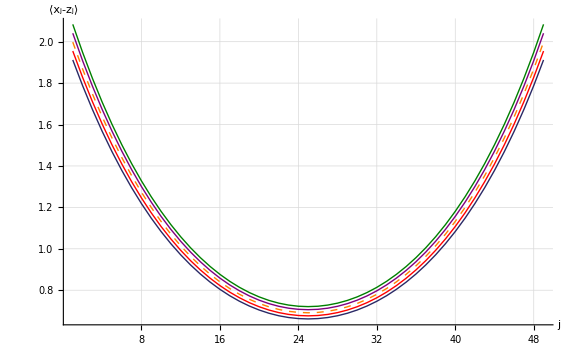
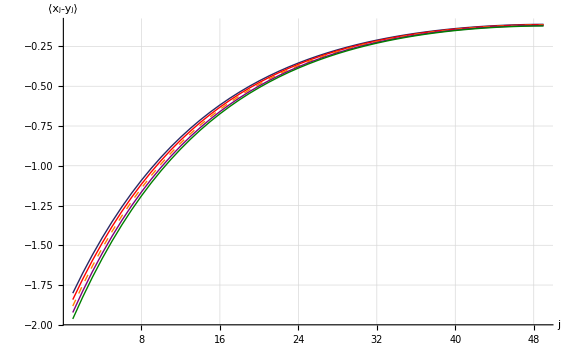

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pxzpair=ListLinePlot[{xzpair[[pos1]],xzpair[[pos2]],xzpair[[pos3]],xzpair[[pos4]],xzpair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-z_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

pxypair=ListLinePlot[{xypair[[pos1]],xypair[[pos2]],xypair[[pos3]],xypair[[pos4]],xypair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-y_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

{pxzpair,pxypair}
```

Analysis

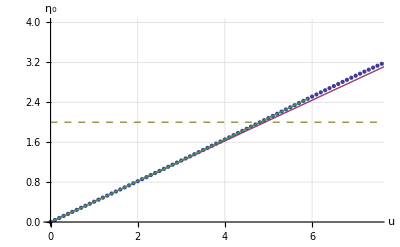

Interpolated Extension = 4.91675

```mathematica
y[x_]:=Subscript[η, B]
MXDp1=Plot[y[x],{x,0,umax Δ/2},PlotStyle->{ColorData[1,3],Dashed}];

MeanAxialDispDataRAW=Flatten[Transpose[Take[Transpose[xzpair],1]]];
maximumValue=Max[MeanAxialDispDataRAW];
positionOfMaximumValue=Flatten[Position[MeanAxialDispDataRAW,maximumValue]][[1]];

MeanAxialDispData = Table[{(i-1)Δ,MeanAxialDispDataRAW[[i]]},{i,1,positionOfMaximumValue}];
MXDp2=ListPlot[MeanAxialDispData];

model=a x  ;
MXDpara=FindFit[Take[MeanAxialDispData,10],model,{a},x];
mxd[u_]:=a u /.MXDpara
MXDp3=Plot[mxd[u],{u,0,10},PlotStyle->{ColorData[1,2]}];

mxdInterFunc=Interpolation[MeanAxialDispData];
u=u0/.Quiet[FindRoot[mxd[u0]==Subscript[η, B],{u0,0}]];

MXDp4=Plot[mxdInterFunc[x],{x,0,u+1},PlotStyle->ColorData[1,4]];

Show[{MXDp1,MXDp2,MXDp3,MXDp4},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["η_0",FontSize->fsAxesLabel]}]
Print["Interpolated Extension = ",u,"\n"]
```

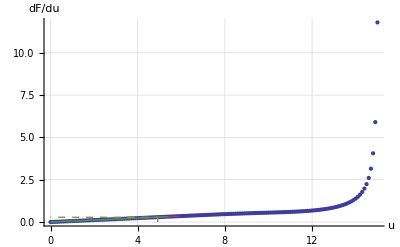

Interpolated Force = 0.280036

```mathematica
FreeEnergyMax=Max[Transpose[dFreeEnergy][[2]]];
positionOfFreeEnergyMax=Flatten[Position[dFreeEnergy,FreeEnergyMax]][[1]];
FreeEnergyData=Table[dFreeEnergy[[i]],{i,1,positionOfFreeEnergyMax}];
FEp1=ListPlot[FreeEnergyData];

model=a x  ;
FEpara=FindFit[Take[FreeEnergyData,10],model,{a},x];
dfe[u0_]:=a u0 /.FEpara
FEp2=Plot[dfe[u0],{u0,0,u+1},PlotStyle->{ColorData[1,2]}];

dfeInterFunc=Interpolation[FreeEnergyData];
F=dfe[u];


FEp3=Plot[dfeInterFunc[x],{x,0,u+.5},PlotStyle->ColorData[1,4]];


fpos={{u,0},{u,F},{0,F}};
FEp4=ListLinePlot[fpos,PlotStyle->{ColorData[1,3],Dashed}];

Show[{FEp1,FEp2,FEp3,FEp4},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF/du",FontSize->fsAxesLabel]}]
Print["Interpolated Force = ",F,"\n"]
```

### Force-Extension

```mathematica
Fc=ToForceDimension[F];
U=ToDimension[u];

Print["\nDimensional Force = ",Fc pN,"\nDimensional Extension = ",U Å,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Fc}},"Table"];
```

Dimensional Force = 124.949 pN
Dimensional Extension = 0.45642 Å